```mathematica
(*Mathematica*)
```

```mathematica
(*PC(n) type 3d polynomials for the Quadratic U(1)*SO(2,C) Mandelbrot 3d recursion*)
```

```mathematica
(* vector recursion in three parts to cycle level 7*)
```

```mathematica
{f[x_],g[y_],h[z_]}={2*x*z+x0,-2*y*z+y0,x^2+y^2-z^2+z0}/.x0->x/.y0->y/.z0->z
```

{x+2 x z,y-2 y z,x^2+y^2+z-z^2}

```mathematica
nr=NestList[f,x,7]
```

{x,x+2 x z,x+2 x z+2 z (x+2 x z),x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z)),x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z))+2 z (x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z))),x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z))+2 z (x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z)))+2 z (x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z))+2 z (x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z)))),x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z))+2 z (x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z)))+2 z (x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z))+2 z (x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z))))+2 z (x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z))+2 z (x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z)))+2 z (x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z))+2 z (x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z))))),x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z))+2 z (x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z)))+2 z (x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z))+2 z (x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z))))+2 z (x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z))+2 z (x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z)))+2 z (x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z))+2 z (x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z)))))+2 z (x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z))+2 z (x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z)))+2 z (x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z))+2 z (x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z))))+2 z (x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z))+2 z (x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z)))+2 z (x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z))+2 z (x+2 x z+2 z (x+2 x z)+2 z (x+2 x z+2 z (x+2 x z))))))}

```mathematica
Length[nr]
```

8

```mathematica
mr=NestList[g,y,7]
```

{y,y-2 y z,y-2 y z-2 z (y-2 y z),y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z)),y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z))-2 z (y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z))),y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z))-2 z (y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z)))-2 z (y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z))-2 z (y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z)))),y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z))-2 z (y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z)))-2 z (y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z))-2 z (y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z))))-2 z (y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z))-2 z (y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z)))-2 z (y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z))-2 z (y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z))))),y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z))-2 z (y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z)))-2 z (y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z))-2 z (y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z))))-2 z (y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z))-2 z (y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z)))-2 z (y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z))-2 z (y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z)))))-2 z (y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z))-2 z (y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z)))-2 z (y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z))-2 z (y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z))))-2 z (y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z))-2 z (y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z)))-2 z (y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z))-2 z (y-2 y z-2 z (y-2 y z)-2 z (y-2 y z-2 z (y-2 y z))))))}

```mathematica
Length[mr]
```

8

```mathematica
lr=NestList[h,z,7]
```

{z,x^2+y^2+z-z^2,2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2,3 x^2+3 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2,4 x^2+4 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2-(3 x^2+3 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2)^2,5 x^2+5 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2-(3 x^2+3 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2)^2-(4 x^2+4 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2-(3 x^2+3 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2)^2)^2,6 x^2+6 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2-(3 x^2+3 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2)^2-(4 x^2+4 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2-(3 x^2+3 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2)^2)^2-(5 x^2+5 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2-(3 x^2+3 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2)^2-(4 x^2+4 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2-(3 x^2+3 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2)^2)^2)^2,7 x^2+7 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2-(3 x^2+3 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2)^2-(4 x^2+4 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2-(3 x^2+3 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2)^2)^2-(5 x^2+5 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2-(3 x^2+3 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2)^2-(4 x^2+4 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2-(3 x^2+3 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2)^2)^2)^2-(6 x^2+6 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2-(3 x^2+3 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2)^2-(4 x^2+4 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2-(3 x^2+3 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2)^2)^2-(5 x^2+5 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2-(3 x^2+3 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2)^2-(4 x^2+4 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2-(3 x^2+3 y^2+z-z^2-(x^2+y^2+z-z^2)^2-(2 x^2+2 y^2+z-z^2-(x^2+y^2+z-z^2)^2)^2)^2)^2)^2)^2}

```mathematica
Length[lr]
```

8

```mathematica
(* solving for cycles Julias *)
```

```mathematica
w={x,y,z}/.NSolve[{nr[[7]]==0,mr[[7]]==0,lr[[7]]==0},{x,y,z}]
```

{{-1.73525+0.0375628 ⅈ,0,-0.491745-0.0487037 ⅈ},{0,0,0.633731+1.32551 ⅈ},{0,-1.52333-0.0973859 ⅈ,0.540241-0.0336964 ⅈ},{0,-1.43717+0.0171777 ⅈ,0.499421-0.00571764 ⅈ},{0,1.39578+0.020717 ⅈ,0.498379-0.000941346 ⅈ},{0,1.38267+0.00995995 ⅈ,0.49315+0.051028 ⅈ},{0,-1.33297+0.028743 ⅈ,0.499699+0.00586373 ⅈ},{0,0,1.19031-0.0846807 ⅈ},{0,0,1.14419-0.327201 ⅈ},{0,0,1.18457-0.110631 ⅈ},{0,0,1.06849+0.517162 ⅈ},{1.27489+0.292449 ⅈ,0,-0.501711-0.00143108 ⅈ},{0,0,1.0386+0.543012 ⅈ},{0,0,0.748542+0.88914 ⅈ},{0,1.28736+0.045338 ⅈ,0.499332-0.0052591 ⅈ},{0,1.28578+0.025013 ⅈ,0.50442-0.00343827 ⅈ},{0,-1.28578+0.0156267 ⅈ,0.499345+0.00597978 ⅈ},{0,-1.28479-0.00577213 ⅈ,0.504918-0.00349241 ⅈ},{0,-1.28307+0.04055 ⅈ,0.504784-0.0033128 ⅈ},{0,-1.28338+0.0238307 ⅈ,0.494875+0.00270813 ⅈ},{0,-1.28124-0.042725 ⅈ,0.499262+0.00597608 ⅈ},{0,1.27941-0.0235575 ⅈ,0.49514-0.00293266 ⅈ},{0,-1.27858+0.0417385 ⅈ,0.504788-0.00330754 ⅈ},{0,-1.27868-0.011004 ⅈ,0.495042-0.00274271 ⅈ},{0,0,0.53302-1.01658 ⅈ},{0,-1.27514+0.0460161 ⅈ,0.499516-0.00588157 ⅈ},{0,-1.27488-0.0259885 ⅈ,0.495049-0.00272317 ⅈ},{0,1.27328-0.0144656 ⅈ,0.499772-0.00502152 ⅈ},{0,1.27239-0.0324751 ⅈ,0.495711-0.00266582 ⅈ},{0,-1.2713-0.0309675 ⅈ,0.499151-0.00514781 ⅈ},{0,-1.26808+0.00535858 ⅈ,0.504947-0.0035012 ⅈ},{0,1.26381-0.0388023 ⅈ,0.499403-0.00528466 ⅈ},{0,-1.25052+0.171974 ⅈ,0.503575-0.00362369 ⅈ},{0,1.26023-0.0352046 ⅈ,0.499706-0.00578793 ⅈ},{0,-1.25568-0.0354862 ⅈ,0.504976+0.00354605 ⅈ},{0,0,0.770367+0.818608 ⅈ},{0,-1.24945-0.0229672 ⅈ,0.494813+0.00279086 ⅈ},{0,3.62667×10^-8-9.89739×10^-8 ⅈ,0.903612-0.664485 ⅈ},{0,0,0.812967-0.772583 ⅈ},{1.22292+0.226139 ⅈ,0,-0.499379+0.0057068 ⅈ},{0,1.23944-0.0409026 ⅈ,0.49933+0.00520444 ⅈ},{1.23578-0.00426893 ⅈ,0,-0.499362-0.0058305 ⅈ},{0,0,0.257646+1.07694 ⅈ},{-1.21705-0.149544 ⅈ,0,-0.500269-0.0000646873 ⅈ},{1.60677×10^-9+7.98642×10^-10 ⅈ,5.08778×10^-9-8.87538×10^-10 ⅈ,0.292525+1.06141 ⅈ},{0,0,0.235546-1.07022 ⅈ},{-1.20588+0.0553131 ⅈ,0,-0.494873-0.00187312 ⅈ},{0,0,0.225487+1.05234 ⅈ},{0,0,0.262743+1.04233 ⅈ},{0,0,0.811126-0.697334 ⅈ},{0,0,0.307171+1.00729 ⅈ},{0,-1.14772+0.134735 ⅈ,0.495034+0.00251745 ⅈ},{0,1.14782+0.133556 ⅈ,0.505089+0.00355098 ⅈ},{0,1.14765-0.133785 ⅈ,0.503994-0.00403321 ⅈ},{1.12189+0.211002 ⅈ,0,-0.504258-0.00311845 ⅈ},{0,0,0.0216103-1.02612 ⅈ},{-1.11534+0.212723 ⅈ,0,-0.499111-0.00521945 ⅈ},{-1.11349-0.219061 ⅈ,0,-0.495262+0.00308381 ⅈ},{-1.11387-0.216492 ⅈ,0,-0.495261+0.00309045 ⅈ},{-1.11487+0.210938 ⅈ,0,-0.498941-0.00623924 ⅈ},{-1.11316-0.216276 ⅈ,0,-0.495262+0.00308966 ⅈ},{-1.1141-0.210241 ⅈ,0,-0.499648+0.00595665 ⅈ},{1.11322-0.214736 ⅈ,0,-0.495007-0.00267617 ⅈ},{-1.11351-0.210996 ⅈ,0,-0.495259+0.00309762 ⅈ},{1.11329-0.209738 ⅈ,0,-0.499261-0.00580688 ⅈ},{1.11307-0.210222 ⅈ,0,-0.499338-0.00590973 ⅈ},{-1.11295-0.21003 ⅈ,0,-0.499668+0.00585744 ⅈ},{1.11302+0.209677 ⅈ,0,-0.499436+0.00595398 ⅈ},{-1.11408-0.202629 ⅈ,0,-0.504801+0.00346828 ⅈ},{-1.1122+0.208245 ⅈ,0,-0.499112-0.00521589 ⅈ},{-1.11224+0.206993 ⅈ,0,-0.494863-0.00242246 ⅈ},{-1.1111+0.202354 ⅈ,0,-0.494867-0.00242495 ⅈ},{0,0,1.00525},{0,0,1.00488+8.52919×10^-9 ⅈ},{0,0,1.00473+4.99963×10^-9 ⅈ},{0,0,1.0047},{0,0,0.498689+0.865594 ⅈ},{0,0,0.500646-0.863638 ⅈ},{0,0,0.50218+0.862549 ⅈ},{0,0,0.499023-0.863533 ⅈ},{-1.07493-0.211186 ⅈ,0,-0.501026+0.00261556 ⅈ},{0,0.892839-0.618664 ⅈ,0.504869+0.0035896 ⅈ},{0,0.892836-0.618666 ⅈ,0.504869+0.00359066 ⅈ},{0,0,-0.0552511+0.974811 ⅈ},{0,0,-0.045963+0.973836 ⅈ},{-1.31381×10^-7+1.25189×10^-7 ⅈ,-2.78801×10^-8-2.22719×10^-7 ⅈ,0.0427201+0.971274 ⅈ},{0,-0.894266-0.576235 ⅈ,0.498966+0.00584475 ⅈ},{0,0,0.111531+0.940279 ⅈ},{0,0,-0.0974668-0.928179 ⅈ},{7.7219×10^-8-3.28184×10^-8 ⅈ,-5.68436×10^-6+2.24269×10^-6 ⅈ,0.692278+0.617671 ⅈ},{0,0.815995-0.628982 ⅈ,0.500594-0.00569268 ⅈ},{0,-0.815992+0.628981 ⅈ,0.500345-0.0056217 ⅈ},{0,-0.815991+0.62898 ⅈ,0.500344-0.00561786 ⅈ},{0,0.815989-0.628955 ⅈ,0.495425-0.00279577 ⅈ},{6.33701×10^-8-4.88458×10^-8 ⅈ,-2.81311×10^-6+3.25377×10^-6 ⅈ,0.647725+0.65799 ⅈ},{0,0.883639+0.522523 ⅈ,0.499123+0.00519427 ⅈ},{-1.86948×10^-7+1.32601×10^-7 ⅈ,-1.86511×10^-7-1.64305×10^-7 ⅈ,0.0175348-0.919851 ⅈ},{-3.60494×10^-8+5.57097×10^-9 ⅈ,-1.12056×10^-8-8.92228×10^-9 ⅈ,-0.132278+0.87587 ⅈ},{0,0.899712-0.375936 ⅈ,0.54611+0.0357639 ⅈ},{1.48121×10^-8-3.33387×10^-9 ⅈ,6.21393×10^-9-4.2392×10^-9 ⅈ,-0.038492+0.87548 ⅈ},{0,0.854859-0.458191 ⅈ,0.504357+0.00342758 ⅈ},{-4.92533×10^-8-4.15937×10^-8 ⅈ,-6.93935×10^-9-3.34055×10^-8 ⅈ,-0.0708405+0.869094 ⅈ},{0,-0.851219+0.462325 ⅈ,0.494432-0.00246933 ⅈ},{0,0.848426-0.464166 ⅈ,0.499131-0.00610711 ⅈ},{0,0.848315-0.463972 ⅈ,0.505087-0.00317239 ⅈ},{0,0.848311-0.463972 ⅈ,0.504902-0.00333198 ⅈ},{0,0.848312-0.463969 ⅈ,0.505062-0.00315039 ⅈ},{0,-0.848311+0.463969 ⅈ,0.504906-0.00319768 ⅈ},{0,-0.84831+0.463971 ⅈ,0.504912-0.00320213 ⅈ},{0,-0.848309+0.463971 ⅈ,0.50491-0.00320051 ⅈ},{0,-0.848309-0.46397 ⅈ,0.504336+0.00321417 ⅈ},{0,-0.848309+0.463968 ⅈ,0.504368-0.00317362 ⅈ},{0,0.848308-0.463968 ⅈ,0.504413-0.00307517 ⅈ},{0,0.848306-0.463971 ⅈ,0.504414-0.00307549 ⅈ},{0,-0.848304+0.463961 ⅈ,0.494622+0.00299686 ⅈ},{0,-0.848304+0.463961 ⅈ,0.494622+0.00299716 ⅈ},{0,0.848303+0.463961 ⅈ,0.494583-0.00315119 ⅈ},{0,-0.848304+0.46396 ⅈ,0.494574+0.00302534 ⅈ},{0,0.848302+0.463962 ⅈ,0.494775-0.00337041 ⅈ},{0,0.848302+0.46394 ⅈ,0.504521-0.00314777 ⅈ},{0,0.848303-0.463936 ⅈ,0.504875+0.00351447 ⅈ},{0,0.848299-0.463941 ⅈ,0.50415+0.00312562 ⅈ},{0,0.848301-0.463937 ⅈ,0.504875+0.00351419 ⅈ},{0,0.848299+0.46394 ⅈ,0.504515-0.00314364 ⅈ},{0,-0.8483+0.463939 ⅈ,0.504823+0.00333393 ⅈ},{0,0.8483-0.463937 ⅈ,0.504852+0.00349476 ⅈ},{0,0.848299-0.46394 ⅈ,0.50439+0.00340251 ⅈ},{0,0.848299-0.463939 ⅈ,0.504811+0.00345786 ⅈ},{0,0.848298+0.46394 ⅈ,0.504517-0.00314441 ⅈ},{0,0.848301-0.463935 ⅈ,0.504874+0.00351444 ⅈ},{0,0.8483+0.463937 ⅈ,0.504515-0.00314282 ⅈ},{0,0.8483-0.463935 ⅈ,0.504875+0.00351422 ⅈ},{0,0.8483-0.463935 ⅈ,0.50493+0.00370367 ⅈ},{0,0.848298-0.463936 ⅈ,0.504852+0.0034944 ⅈ},{0,-0.848299+0.463935 ⅈ,0.504813+0.00332689 ⅈ},{0,0.848298-0.463936 ⅈ,0.504872+0.00351173 ⅈ},{0,0.848298-0.463936 ⅈ,0.504873+0.00351375 ⅈ},{0,0.848287+0.463955 ⅈ,0.499642-0.00526099 ⅈ},{0,0.848298-0.463935 ⅈ,0.504874+0.00351312 ⅈ},{0,0.848286-0.463954 ⅈ,0.499699+0.00520918 ⅈ},{0,-0.848283-0.463959 ⅈ,0.499346-0.00583336 ⅈ},{0,-0.848285+0.463955 ⅈ,0.499487+0.00540969 ⅈ},{0,0.848284+0.463956 ⅈ,0.499859-0.00557769 ⅈ},{0,0.848282-0.463961 ⅈ,0.499233-0.00526591 ⅈ},{0,-0.848284+0.463956 ⅈ,0.4999+0.00526639 ⅈ},{0,0.84829-0.463944 ⅈ,0.495475-0.00270284 ⅈ},{0,-0.848291+0.463941 ⅈ,0.494409-0.00294621 ⅈ},{0,-0.84828-0.463963 ⅈ,0.499335+0.00532395 ⅈ},{0,-0.848292-0.463941 ⅈ,0.494627+0.00288724 ⅈ},{0,-0.848291+0.463941 ⅈ,0.494412-0.00294464 ⅈ},{0,-0.84828+0.463963 ⅈ,0.499303-0.00528799 ⅈ},{0,0.848279+0.463964 ⅈ,0.499322+0.00568668 ⅈ},{0,-0.84828+0.463962 ⅈ,0.499402-0.00537223 ⅈ},{0,0.848277-0.463967 ⅈ,0.499661-0.0063121 ⅈ},{0,-0.848278+0.463963 ⅈ,0.499474-0.00533701 ⅈ},{0,-0.848279+0.463962 ⅈ,0.499054-0.00526619 ⅈ},{0,-0.848282+0.463957 ⅈ,0.499379+0.00609684 ⅈ},{0,0.84828-0.46396 ⅈ,0.499506-0.00528898 ⅈ},{0,0.848282+0.463957 ⅈ,0.499557-0.00614035 ⅈ},{0,0.848282-0.463957 ⅈ,0.499259+0.00566801 ⅈ},{0,-0.84829-0.46394 ⅈ,0.494517+0.00294645 ⅈ},{0,-0.848291-0.463939 ⅈ,0.49463+0.0028857 ⅈ},{0,0.848291-0.463938 ⅈ,0.494672-0.00326044 ⅈ},{0,-0.848282-0.463954 ⅈ,0.499717-0.00594158 ⅈ},{0,-0.84828-0.463956 ⅈ,0.499394-0.0060066 ⅈ},{0,0.848275-0.463965 ⅈ,0.499555-0.00640309 ⅈ},{0,0.848279-0.463956 ⅈ,0.499166+0.00617702 ⅈ},{0,-0.84828-0.463955 ⅈ,0.499713-0.00596673 ⅈ},{0,0.848359-0.463694 ⅈ,0.494372-0.00285769 ⅈ},{0,0.848296-0.463709 ⅈ,0.494336-0.00287635 ⅈ},{0,0,-0.123197-0.860339 ⅈ},{0,-0.849239+0.461367 ⅈ,0.494337-0.0025114 ⅈ},{0,0.854533+0.450124 ⅈ,0.503996+0.00336167 ⅈ},{0,0.772275+0.564173 ⅈ,0.504874+0.00362256 ⅈ},{0,-0.772274-0.564173 ⅈ,0.504856+0.00350944 ⅈ},{0,0.772274-0.564172 ⅈ,0.504901-0.00350409 ⅈ},{0,0.772272+0.56417 ⅈ,0.504879+0.00362575 ⅈ},{0,-0.772269+0.564173 ⅈ,0.50438-0.00313888 ⅈ},{0,0.772268+0.564168 ⅈ,0.494652-0.00312025 ⅈ},{0,0.772267+0.564168 ⅈ,0.494649-0.00329933 ⅈ},{0,-0.772267-0.564169 ⅈ,0.494744-0.00316164 ⅈ},{0,-0.772267-0.564167 ⅈ,0.494744-0.00316076 ⅈ},{0,-0.772266-0.564168 ⅈ,0.494861-0.00301465 ⅈ},{0,-0.772266-0.564168 ⅈ,0.494862-0.00301432 ⅈ},{0,0.772267+0.564166 ⅈ,0.494438-0.00292456 ⅈ},{0,-0.772266-0.564168 ⅈ,0.494863-0.00301396 ⅈ},{0,-0.772265-0.564167 ⅈ,0.494772-0.00291135 ⅈ},{0,-0.772245-0.564194 ⅈ,0.499441-0.0060297 ⅈ},{0,0.772247-0.564191 ⅈ,0.499389+0.00542452 ⅈ},{0,-0.772243-0.564195 ⅈ,0.499612-0.00620446 ⅈ},{0,-0.772264-0.564167 ⅈ,0.494747-0.00252206 ⅈ},{0,0.772245-0.564191 ⅈ,0.49927+0.0053986 ⅈ},{0,-0.772264-0.564166 ⅈ,0.49476-0.00251584 ⅈ},{0,-0.772263-0.564166 ⅈ,0.494759-0.00251652 ⅈ},{0,0.772246+0.56419 ⅈ,0.499779-0.00542481 ⅈ},{0,-0.772246+0.56419 ⅈ,0.499474+0.00530845 ⅈ},{0,0.772244+0.564192 ⅈ,0.499615-0.00563987 ⅈ},{0,-0.77224-0.564197 ⅈ,0.499281+0.00597918 ⅈ},{0,0.772241+0.564194 ⅈ,0.499341+0.00526359 ⅈ},{0,0.772241+0.564194 ⅈ,0.499428+0.00526348 ⅈ},{0,-0.772239-0.564197 ⅈ,0.499179+0.00590026 ⅈ},{0,-0.772244+0.564189 ⅈ,0.499631+0.00524833 ⅈ},{0,-0.772241+0.564193 ⅈ,0.49934-0.00514953 ⅈ},{0,-0.772235-0.564163 ⅈ,0.50429-0.00297589 ⅈ},{0,0.772235+0.564162 ⅈ,0.504259-0.00301578 ⅈ},{0,-0.772231-0.564161 ⅈ,0.494652+0.00283238 ⅈ},{0,-0.77223+0.564161 ⅈ,0.49454-0.00272258 ⅈ},{0,0.772228-0.564162 ⅈ,0.494503-0.00312655 ⅈ},{0,-0.77223-0.564159 ⅈ,0.504988-0.0034268 ⅈ},{0,0.77223+0.564157 ⅈ,0.505286-0.00333459 ⅈ},{0,-0.772123-0.564241 ⅈ,0.494408+0.00268618 ⅈ},{0.939601-0.164905 ⅈ,0,-0.505143-0.00342318 ⅈ},{0.939583-0.164919 ⅈ,0,-0.505143-0.00342363 ⅈ},{0.763756-0.567969 ⅈ,0,-0.490765-0.00515081 ⅈ},{-0.934802+0.170873 ⅈ,0,-0.504981-0.00345515 ⅈ},{-6.30351×10^-8+3.21134×10^-7 ⅈ,0.89382+0.301409 ⅈ,0.487198+0.115775 ⅈ},{0.92289+0.17881 ⅈ,0,-0.505162-0.00386853 ⅈ},{0.921165-0.182189 ⅈ,0,-0.499439+0.00619018 ⅈ},{0.921133-0.182254 ⅈ,0,-0.499331+0.00624554 ⅈ},{-0.921124+0.18222 ⅈ,0,-0.499297+0.00614443 ⅈ},{-0.921071+0.182226 ⅈ,0,-0.499298+0.00615064 ⅈ},{0.920982+0.182183 ⅈ,0,-0.499215-0.00598716 ⅈ},{0.920959+0.18223 ⅈ,0,-0.499143-0.00600866 ⅈ},{-0.92079-0.182309 ⅈ,0,-0.498859-0.00596865 ⅈ},{-0.920656-0.18205 ⅈ,0,-0.498968-0.00537179 ⅈ},{-0.920586-0.181979 ⅈ,0,-0.498955-0.00540646 ⅈ},{0.919801-0.17551 ⅈ,0,-0.504871-0.00341915 ⅈ},{0.919757-0.175329 ⅈ,0,-0.505001-0.00368996 ⅈ},{-0.919587+0.175223 ⅈ,0,-0.504911-0.00398937 ⅈ},{-0.917633+0.182504 ⅈ,0,-0.494771+0.00285521 ⅈ},{0.917513+0.182428 ⅈ,0,-0.494697-0.0025431 ⅈ},{0.908794+0.221711 ⅈ,0,-0.499871+0.00371623 ⅈ},{-0.916818-0.17676 ⅈ,0,-0.499954+0.00521201 ⅈ},{0.916599-0.176898 ⅈ,0,-0.499541-0.00524246 ⅈ},{0.915721-0.179598 ⅈ,0,-0.494891-0.00304044 ⅈ},{-0.915582+0.179908 ⅈ,0,-0.495038-0.00253639 ⅈ},{0.916209+0.176393 ⅈ,0,-0.499592+0.00615071 ⅈ},{0.915537-0.179662 ⅈ,0,-0.494813-0.00308482 ⅈ},{0.915532-0.179667 ⅈ,0,-0.494813-0.00308621 ⅈ},{0.915532-0.179663 ⅈ,0,-0.494813-0.00308562 ⅈ},{-0.915243-0.179519 ⅈ,0,-0.495073+0.00345009 ⅈ},{0.915786+0.176453 ⅈ,0,-0.499736+0.00612005 ⅈ},{-0.915583-0.176401 ⅈ,0,-0.49995+0.0061996 ⅈ},{-0.89879-0.228385 ⅈ,0,-0.495385+0.00347234 ⅈ},{-0.898768-0.228402 ⅈ,0,-0.495388+0.00346921 ⅈ},{-0.909355+0.171343 ⅈ,0,-0.499357-0.00539217 ⅈ},{0.897593+0.223036 ⅈ,0,-0.495008+0.00325162 ⅈ},{0.897592+0.223037 ⅈ,0,-0.495007+0.00325128 ⅈ},{0.897458+0.22315 ⅈ,0,-0.495019+0.00324291 ⅈ},{0.897261+0.223318 ⅈ,0,-0.495038+0.00323381 ⅈ},{-0.897835-0.195429 ⅈ,0,-0.499497+0.00622871 ⅈ},{0.88934-0.222936 ⅈ,0,-0.499775-0.00361054 ⅈ},{0.889326-0.22294 ⅈ,0,-0.499758-0.00361961 ⅈ},{0.891162-0.189574 ⅈ,0,-0.499565-0.00622154 ⅈ},{0.891157-0.189573 ⅈ,0,-0.499565-0.00622153 ⅈ},{0.853907-0.238222 ⅈ,0,-0.499326-0.00201082 ⅈ},{0,0,-0.213564+0.767696 ⅈ},{0.845356+0.257353 ⅈ,0,-0.499772+0.00602879 ⅈ},{0.844591+0.259778 ⅈ,0,-0.500485+0.00176554 ⅈ},{-0.84051-0.262281 ⅈ,0,-0.500287+0.00155936 ⅈ},{0,0,-0.215399-0.759165 ⅈ},{-0.840839-0.249135 ⅈ,0,-0.501874+0.000797399 ⅈ},{8.27526×10^-8+4.55497×10^-7 ⅈ,-1.24765×10^-6-4.36883×10^-7 ⅈ,0.154465-0.772788 ⅈ},{-0.848432+0.214829 ⅈ,0,-0.495073-0.00272708 ⅈ},{-0.848424+0.214829 ⅈ,0,-0.495073-0.00272806 ⅈ},{0.837445+0.251221 ⅈ,0,-0.503277+0.00204623 ⅈ},{-0.837255-0.246816 ⅈ,0,-0.500017+0.00522049 ⅈ},{0,0,-0.230628+0.747012 ⅈ},{0.825426-0.257076 ⅈ,0,-0.499559-0.00620589 ⅈ},{-0.820825+0.255772 ⅈ,0,-0.50517-0.00363677 ⅈ},{-0.820825+0.255771 ⅈ,0,-0.50517-0.00363705 ⅈ},{-0.820824+0.255772 ⅈ,0,-0.50517-0.0036375 ⅈ},{-0.821256+0.25054 ⅈ,0,-0.499343-0.00543591 ⅈ},{0.808209+0.278518 ⅈ,0,-0.501091+0.00115674 ⅈ},{0.816056-0.251398 ⅈ,0,-0.504646-0.00319013 ⅈ},{0.816051-0.251397 ⅈ,0,-0.504645-0.00318792 ⅈ},{0.816029-0.251388 ⅈ,0,-0.504642-0.00318657 ⅈ},{0.816028-0.251389 ⅈ,0,-0.504641-0.00318695 ⅈ},{-0.81121+0.266343 ⅈ,0,-0.497878-0.00109207 ⅈ},{-0.815995+0.25104 ⅈ,0,-0.504523-0.00321712 ⅈ},{-0.815869+0.251 ⅈ,0,-0.504511-0.00320679 ⅈ},{0.814161-0.255904 ⅈ,0,-0.505237+0.00385156 ⅈ},{0.814034+0.25599 ⅈ,0,-0.505046-0.00385482 ⅈ},{-0.813612+0.255794 ⅈ,0,-0.49465-0.00294163 ⅈ},{0.813484-0.256109 ⅈ,0,-0.504392+0.00360032 ⅈ},{-0.813282-0.256183 ⅈ,0,-0.504159-0.00354821 ⅈ},{0.813293+0.256097 ⅈ,0,-0.504231-0.00345422 ⅈ},{0.813292+0.256096 ⅈ,0,-0.504231-0.00345362 ⅈ},{0.813294+0.25609 ⅈ,0,-0.504229-0.00344763 ⅈ},{0.813291+0.256096 ⅈ,0,-0.504232-0.00345261 ⅈ},{0.813292+0.256092 ⅈ,0,-0.504228-0.00344848 ⅈ},{0.813292+0.25609 ⅈ,0,-0.504226-0.00344716 ⅈ},{-0.811163+0.262614 ⅈ,0,-0.498957+0.00617995 ⅈ},{-0.811157+0.262613 ⅈ,0,-0.498956+0.00618 ⅈ},{0.810928+0.260082 ⅈ,0,-0.498988-0.00597306 ⅈ},{-0.810759-0.260292 ⅈ,0,-0.498665-0.00607398 ⅈ},{0.810606+0.259831 ⅈ,0,-0.498851-0.00545363 ⅈ},{0.80992-0.259573 ⅈ,0,-0.499196+0.00548164 ⅈ},{0,0,-0.247421+0.722755 ⅈ},{-0.803238-0.276603 ⅈ,0,-0.499199+0.00197525 ⅈ},{-0.806609-0.266334 ⅈ,0,-0.501208+0.00088016 ⅈ},{0.81082+0.251488 ⅈ,0,-0.504398+0.0033205 ⅈ},{-0.810392-0.251507 ⅈ,0,-0.504341+0.00328846 ⅈ},{-0.810385-0.251517 ⅈ,0,-0.504326+0.00328339 ⅈ},{0.81042+0.251375 ⅈ,0,-0.504461+0.00340629 ⅈ},{0.810413+0.251388 ⅈ,0,-0.504444+0.00339706 ⅈ},{-0.806791+0.259652 ⅈ,0,-0.495079+0.00253735 ⅈ},{0.806339+0.259776 ⅈ,0,-0.494428-0.002457 ⅈ},{0.806248+0.259919 ⅈ,0,-0.494237-0.00254316 ⅈ},{-0.806139-0.259446 ⅈ,0,-0.494453-0.00198556 ⅈ},{0.808352-0.251342 ⅈ,0,-0.502351-0.00485528 ⅈ},{0.801698+0.270881 ⅈ,0,-0.497584+0.00168123 ⅈ},{-0.808234-0.245276 ⅈ,0,-0.49527+0.00356663 ⅈ},{0.804136-0.256511 ⅈ,0,-0.494436-0.0024493 ⅈ},{-0.807524-0.243627 ⅈ,0,-0.49506+0.00373505 ⅈ},{-0.8074-0.243314 ⅈ,0,-0.495026+0.00376187 ⅈ},{0.803548+0.253805 ⅈ,0,-0.504309-0.00353403 ⅈ},{0.804462+0.246929 ⅈ,0,-0.494868+0.00328615 ⅈ},{0.792782+0.275698 ⅈ,0,-0.504729-0.00394132 ⅈ},{0,0,-0.264035-0.703248 ⅈ},{-0.789616+0.268559 ⅈ,0,-0.498766-0.00110885 ⅈ},{0,0.54492+0.62842 ⅈ,0.499644-0.00642781 ⅈ},{0,0.544922-0.628417 ⅈ,0.499352+0.00574369 ⅈ},{0,-0.544921+0.628415 ⅈ,0.49962+0.00560163 ⅈ},{0,-0.544938+0.6284 ⅈ,0.504459-0.00338368 ⅈ},{0,0.544937-0.6284 ⅈ,0.504406-0.00323337 ⅈ},{0,0.544942+0.628395 ⅈ,0.494486-0.00326016 ⅈ},{0,-0.544936-0.6284 ⅈ,0.50422+0.00322979 ⅈ},{0,0.544936+0.6284 ⅈ,0.504251+0.0031563 ⅈ},{0,-0.544918+0.628414 ⅈ,0.499774-0.00553872 ⅈ},{0,-0.544913-0.628416 ⅈ,0.49914+0.00604389 ⅈ},{0,0.544916+0.628413 ⅈ,0.499365+0.00537191 ⅈ},{0,-0.544915+0.628413 ⅈ,0.499281-0.00547091 ⅈ},{0,-0.54492-0.628381 ⅈ,0.506214-0.00117526 ⅈ},{0,-0.544912-0.628387 ⅈ,0.494728+0.00262911 ⅈ},{0,-0.544912-0.628387 ⅈ,0.494728+0.0026298 ⅈ},{0,-0.544912-0.628387 ⅈ,0.494728+0.00262948 ⅈ},{0,0.544909-0.628385 ⅈ,0.494415-0.0031249 ⅈ},{-0.795173-0.241259 ⅈ,0,-0.504997+0.00303441 ⅈ},{0.798418-0.205567 ⅈ,0,-0.504881+0.00377659 ⅈ},{0.798318-0.205315 ⅈ,0,-0.504881+0.0037767 ⅈ},{0.78546+0.246398 ⅈ,0,-0.505102+0.0031474 ⅈ},{-0.775992-0.26735 ⅈ,0,-0.50124-0.00184034 ⅈ},{-0.774478-0.269719 ⅈ,0,-0.49813-0.00293566 ⅈ},{-0.775553-0.265193 ⅈ,0,-0.50239+0.000465972 ⅈ},{0.781038+0.24727 ⅈ,0,-0.499804+0.00547502 ⅈ},{-0.773176-0.267855 ⅈ,0,-0.498391-4.65731×10^-6 ⅈ},{0,0.502144-0.645986 ⅈ,0.499405+0.00229288 ⅈ},{-0.777658-0.254009 ⅈ,0,-0.50015+0.00577823 ⅈ},{-0.773276-0.267001 ⅈ,0,-0.498983+0.000458956 ⅈ},{0,0,-0.284172+0.677668 ⅈ},{0.775816-0.256424 ⅈ,0,-0.50409+0.00319917 ⅈ},{-0.77194-0.267166 ⅈ,0,-0.497621+0.00127325 ⅈ},{-0.771262-0.266965 ⅈ,0,-0.497249+0.00218417 ⅈ},{-0.771958+0.261879 ⅈ,0,-0.498018+0.000922011 ⅈ},{-0.77176+0.261951 ⅈ,0,-0.497783+0.000811886 ⅈ},{-0.771715+0.261566 ⅈ,0,-0.497998+0.000963431 ⅈ},{-0.769603-0.261412 ⅈ,0,-0.495031+0.00392256 ⅈ},{-0.772691-0.252063 ⅈ,0,-0.495523+0.00351418 ⅈ},{0.770225+0.257624 ⅈ,0,-0.494896+0.00338136 ⅈ},{0.770662+0.256027 ⅈ,0,-0.49499+0.00332053 ⅈ},{0.766584-0.267747 ⅈ,0,-0.501918+0.0016728 ⅈ},{0.766491-0.267682 ⅈ,0,-0.501908+0.00156195 ⅈ},{0.766377-0.267655 ⅈ,0,-0.501825+0.00145714 ⅈ},{0.769123+0.259359 ⅈ,0,-0.500756+0.00233966 ⅈ},{0,0.484163-0.650699 ⅈ,0.498273-0.00159528 ⅈ},{0.784948+0.203889 ⅈ,0,-0.494464-0.00239214 ⅈ},{0,-0.498687+0.638365 ⅈ,0.498673+0.00560269 ⅈ},{-0.766395+0.253945 ⅈ,0,-0.497714+0.000943637 ⅈ},{0,0.494816-0.630185 ⅈ,0.499505+0.00555887 ⅈ},{0,0,-0.306001-0.649871 ⅈ},{0,0,-0.295817-0.654433 ⅈ},{0,0.494816+0.62629 ⅈ,0.499687-0.0065067 ⅈ},{0,-0.494816-0.626288 ⅈ,0.499602-0.00622702 ⅈ},{0,-0.494816+0.626288 ⅈ,0.499673+0.00620529 ⅈ},{0,0.494818-0.626284 ⅈ,0.499417+0.00545429 ⅈ},{0,0.494811-0.626287 ⅈ,0.499476-0.00605731 ⅈ},{0,-0.494831+0.626268 ⅈ,0.504432-0.00336965 ⅈ},{0,-0.494831+0.626268 ⅈ,0.504432-0.00336919 ⅈ},{0,-0.494831+0.626268 ⅈ,0.504432-0.00336942 ⅈ},{0,-0.494831+0.626268 ⅈ,0.504396-0.00333341 ⅈ},{0,-0.494831+0.626268 ⅈ,0.504394-0.00333128 ⅈ},{0,-0.494831+0.626268 ⅈ,0.504361-0.00329913 ⅈ},{0,-0.494811+0.626283 ⅈ,0.499323-0.00541299 ⅈ},{0,0.494811+0.626283 ⅈ,0.499321+0.00541468 ⅈ},{0,0.49483-0.626268 ⅈ,0.504359-0.00318528 ⅈ},{0,-0.494835+0.626264 ⅈ,0.494505+0.00334012 ⅈ},{0,0.494835+0.626264 ⅈ,0.494524-0.0032928 ⅈ},{0,-0.49481-0.626283 ⅈ,0.499095+0.00554294 ⅈ},{0,-0.494802-0.626261 ⅈ,0.50502-0.00327521 ⅈ},{0,-0.494802-0.626261 ⅈ,0.505019-0.00327457 ⅈ},{0,-0.494802-0.626261 ⅈ,0.505021-0.0032755 ⅈ},{0,-0.494802+0.626261 ⅈ,0.50507+0.00329821 ⅈ},{0,0.494802+0.62626 ⅈ,0.505174-0.0033225 ⅈ},{0,0.494802+0.62626 ⅈ,0.505177-0.00332568 ⅈ},{0,0.494802+0.62626 ⅈ,0.505177-0.00332495 ⅈ},{0,0.494802-0.626258 ⅈ,0.494522-0.00312264 ⅈ},{0,0.491615-0.628299 ⅈ,0.498941-0.00602329 ⅈ},{-0.752478-0.263109 ⅈ,0,-0.497096-0.000937931 ⅈ},{-0.752312-0.262893 ⅈ,0,-0.497116-0.000893255 ⅈ},{-0.761538+0.229202 ⅈ,0,-0.498974+0.00528303 ⅈ},{0.754632-0.250998 ⅈ,0,-0.501267-0.00128321 ⅈ},{0,-0.491481+0.622939 ⅈ,0.505036-0.00389413 ⅈ},{0.759043-0.229837 ⅈ,0,-0.499126+0.00540966 ⅈ},{0,-0.497279+0.617552 ⅈ,0.49974+0.00651841 ⅈ},{0,-0.49725+0.617527 ⅈ,0.499743+0.00650307 ⅈ},{0.758852-0.229439 ⅈ,0,-0.499103+0.00550186 ⅈ},{0,0.497491-0.616827 ⅈ,0.499468+0.00644395 ⅈ},{0,-0.471842+0.636141 ⅈ,0.499898-0.00188806 ⅈ},{0,0.501523-0.612342 ⅈ,0.495153-0.00253866 ⅈ},{0,0.46977-0.636178 ⅈ,0.499792-0.0019371 ⅈ},{-0.754191-0.230424 ⅈ,0,-0.494817-0.00169289 ⅈ},{0,0.495146-0.613259 ⅈ,0.499285-0.00551618 ⅈ},{0,0.495145-0.61326 ⅈ,0.499286-0.00551462 ⅈ},{0,-0.495448+0.612682 ⅈ,0.499064-0.00590069 ⅈ},{0.751534+0.230327 ⅈ,0,-0.504264-0.00371814 ⅈ},{-0.749972+0.234544 ⅈ,0,-0.504868+0.00389968 ⅈ},{-0.747758+0.240943 ⅈ,0,-0.50523-0.00356969 ⅈ},{0.749463-0.234542 ⅈ,0,-0.505063+0.00399373 ⅈ},{0.749464-0.234539 ⅈ,0,-0.505063+0.00399251 ⅈ},{0.749529-0.234312 ⅈ,0,-0.505033+0.00396254 ⅈ},{0.749606-0.234014 ⅈ,0,-0.504994+0.00392381 ⅈ},{-0.750851-0.229849 ⅈ,0,-0.504213-0.00382742 ⅈ},{-0.750813-0.229872 ⅈ,0,-0.504216-0.00383184 ⅈ},{0.750681-0.227439 ⅈ,0,-0.504534-0.00296203 ⅈ},{0.750678-0.227448 ⅈ,0,-0.504532-0.0029642 ⅈ},{0.750683-0.227392 ⅈ,0,-0.50453-0.00296085 ⅈ},{0.750683-0.227392 ⅈ,0,-0.50453-0.00296078 ⅈ},{0.750684-0.227374 ⅈ,0,-0.504529-0.00295866 ⅈ},{0.749534+0.225119 ⅈ,0,-0.498868-0.0052729 ⅈ},{-0.750197-0.219999 ⅈ,0,-0.498624-0.00528441 ⅈ},{-0.7498-0.219949 ⅈ,0,-0.498617-0.0053025 ⅈ},{-0.739667+0.24409 ⅈ,0,-0.498917-0.000621368 ⅈ},{0.73889-0.24527 ⅈ,0,-0.4997-0.00623444 ⅈ},{-0.737122+0.248042 ⅈ,0,-0.499431-0.00609817 ⅈ},{0.733594-0.257733 ⅈ,0,-0.499285+0.00438178 ⅈ},{-0.736147+0.249856 ⅈ,0,-0.499404-0.00622214 ⅈ},{0.735725+0.250575 ⅈ,0,-0.49847-0.00165206 ⅈ},{-0.738311+0.239949 ⅈ,0,-0.50059-0.00185194 ⅈ},{0,-0.477387+0.610598 ⅈ,0.494208-0.00274086 ⅈ},{0,-0.477387+0.610597 ⅈ,0.494208-0.00274089 ⅈ},{-0.739929+0.223693 ⅈ,0,-0.494612+0.00288327 ⅈ},{-0.732972+0.244465 ⅈ,0,-0.499694+0.00209611 ⅈ},{-0.731231-0.248128 ⅈ,0,-0.496365-0.00135156 ⅈ},{-0.729736+0.249234 ⅈ,0,-0.495156-0.00286007 ⅈ},{0.72986-0.247839 ⅈ,0,-0.494869-0.00320672 ⅈ},{0.735626+0.229221 ⅈ,0,-0.49899+0.00649105 ⅈ},{0.73776+0.221322 ⅈ,0,-0.494005+0.000961112 ⅈ},{-0.729954+0.245727 ⅈ,0,-0.49567+0.00198935 ⅈ},{-0.73116+0.24143 ⅈ,0,-0.499214+0.00369668 ⅈ},{0,0,-0.32039+0.612108 ⅈ},{0.724611-0.241238 ⅈ,0,-0.499474+0.0022608 ⅈ},{0.722799+0.240916 ⅈ,0,-0.498891-0.00454015 ⅈ},{0.716106+0.247328 ⅈ,0,-0.499036-0.00159485 ⅈ},{-0.714115-0.241935 ⅈ,0,-0.49916-0.0016988 ⅈ},{0.718129+0.223367 ⅈ,0,-0.504187-0.000710539 ⅈ},{-0.715052-0.231491 ⅈ,0,-0.501346+0.00158493 ⅈ},{0.714351+0.229552 ⅈ,0,-0.49672-0.00361674 ⅈ},{-0.708294-0.245196 ⅈ,0,-0.496195-0.00311131 ⅈ},{0.713553+0.226617 ⅈ,0,-0.497995-0.000441905 ⅈ},{-0.734525+0.138282 ⅈ,0,-0.452525+0.0277768 ⅈ},{1.72665×10^-8-1.74408×10^-8 ⅈ,3.2625×10^-9-5.43479×10^-9 ⅈ,-0.349907-0.56388 ⅈ},{0,0,-0.317335+0.574882 ⅈ},{0.692202-0.231046 ⅈ,0,-0.501801+0.0000486873 ⅈ},{0.69127-0.23038 ⅈ,0,-0.499302-0.000859023 ⅈ},{0.695405+0.216499 ⅈ,0,-0.500196+0.0019752 ⅈ},{0,0,-0.319335-0.569917 ⅈ},{-0.689199+0.227854 ⅈ,0,-0.498534-0.000520297 ⅈ},{-0.685532-0.230792 ⅈ,0,-0.494722+0.00359317 ⅈ},{0.488778+0.532656 ⅈ,0,-0.496464-0.00148102 ⅈ},{0,-0.398675-0.602255 ⅈ,0.494206+0.00267023 ⅈ},{0,0,-0.314282+0.566485 ⅈ},{0.69328+0.191527 ⅈ,0,-0.505256+0.00310597 ⅈ},{0.693279+0.19153 ⅈ,0,-0.505257+0.00310737 ⅈ},{0.682612+0.225702 ⅈ,0,-0.500007+0.00082191 ⅈ},{0.0000193842-0.0000871061 ⅈ,2.45757×10^-10-1.34259×10^-10 ⅈ,-0.598787+0.238796 ⅈ},{0.0000200078-0.0000859196 ⅈ,2.42282×10^-10-1.32063×10^-10 ⅈ,-0.598426+0.238802 ⅈ},{0,0.381163+0.603334 ⅈ,0.494402-0.0034212 ⅈ},{0,-0.381312-0.597168 ⅈ,0.494517-0.00344019 ⅈ},{0,-0.398739-0.584154 ⅈ,0.499715-0.00643334 ⅈ},{0,0.38767+0.590598 ⅈ,0.504665+0.00372007 ⅈ},{0,0.399116+0.582794 ⅈ,0.499753-0.00672968 ⅈ},{0.675217+0.206047 ⅈ,0,-0.49994+0.00645014 ⅈ},{0.000156817+0.0000462887 ⅈ,-2.3662×10^-10+1.69552×10^-10 ⅈ,-0.59614-0.218156 ⅈ},{0,0.399175+0.582156 ⅈ,0.499747-0.00678484 ⅈ},{-0.670272-0.203086 ⅈ,0,-0.498359-0.00552001 ⅈ},{0.67016+0.202284 ⅈ,0,-0.498646-0.0053547 ⅈ},{0,-0.382743+0.583509 ⅈ,0.499707+0.00683445 ⅈ},{-0.677855-0.163919 ⅈ,0,-0.502195+0.00520484 ⅈ},{0,0,-0.324111+0.536661 ⅈ},{-0.662463+0.212579 ⅈ,0,-0.498123+0.00068058 ⅈ},{-0.668462-0.189855 ⅈ,0,-0.495538+0.00382098 ⅈ},{0.665901+0.198209 ⅈ,0,-0.498737+0.000200063 ⅈ},{0,0,0.0584702-0.621803 ⅈ},{0,0,0.0585811-0.621724 ⅈ},{-0.664778-0.195913 ⅈ,0,-0.495315+0.00402005 ⅈ},{0,0.388143-0.572184 ⅈ,0.495059-0.00259561 ⅈ},{0.663083+0.195127 ⅈ,0,-0.495022+0.00350969 ⅈ},{0.662403+0.196167 ⅈ,0,-0.494979+0.00353928 ⅈ},{0,0.389691-0.565684 ⅈ,0.49927-0.00560844 ⅈ},{0,0.389654-0.56567 ⅈ,0.499268-0.00561833 ⅈ},{0,-0.389205+0.565346 ⅈ,0.499049-0.00606112 ⅈ},{0,0,-0.320362+0.525675 ⅈ},{0,-0.351244-0.586326 ⅈ,0.495478-0.00285729 ⅈ},{0,-0.351242-0.586318 ⅈ,0.495479-0.00285764 ⅈ},{0.644985+0.216775 ⅈ,0,-0.494068-0.00230111 ⅈ},{0,0.351492+0.582277 ⅈ,0.495283-0.00289792 ⅈ},{0.646556-0.20144 ⅈ,0,-0.497823-0.000494089 ⅈ},{0,-0.389288-0.554032 ⅈ,0.498997+0.00551989 ⅈ},{0,-0.34677-0.58156 ⅈ,0.499772-0.00484205 ⅈ},{0,-0.34676-0.581534 ⅈ,0.499772-0.00484129 ⅈ},{0,0.379004-0.559786 ⅈ,0.499477+0.00592352 ⅈ},{0,-0.38946-0.552301 ⅈ,0.49896+0.00563372 ⅈ},{0,0.388205+0.552602 ⅈ,0.499153+0.00572833 ⅈ},{-0.639812+0.210842 ⅈ,0,-0.49699+0.00455641 ⅈ},{0.641512-0.197908 ⅈ,0,-0.500303-0.000314852 ⅈ},{0,0.00436692+0.0144757 ⅈ,0.597153+0.067573 ⅈ},{-0.639785+0.179185 ⅈ,0,-0.505359-0.00347378 ⅈ},{-0.639783+0.17919 ⅈ,0,-0.505359-0.00347328 ⅈ},{-0.639787+0.179176 ⅈ,0,-0.505359-0.00347107 ⅈ},{-0.639785+0.179178 ⅈ,0,-0.505358-0.00347234 ⅈ},{-0.639784+0.179172 ⅈ,0,-0.505358-0.00347276 ⅈ},{0.630448-0.180426 ⅈ,0,-0.49995-0.00632056 ⅈ},{0.630468-0.180355 ⅈ,0,-0.49995-0.00631716 ⅈ},{-0.628999+0.184127 ⅈ,0,-0.499667-0.00611826 ⅈ},{0,-0.357269-0.548975 ⅈ,0.504384+0.00357214 ⅈ},{0,0.357239+0.548902 ⅈ,0.504684+0.00373272 ⅈ},{0,-0.356894+0.549036 ⅈ,0.498574-0.00670391 ⅈ},{0,-0.356884+0.549023 ⅈ,0.503819+0.00537249 ⅈ},{0,0.356874+0.548971 ⅈ,0.505657-0.00351604 ⅈ},{0,0.356874+0.548971 ⅈ,0.505657-0.00351544 ⅈ},{0,0.356872+0.54897 ⅈ,0.505651-0.00351034 ⅈ},{0,0.356863+0.548969 ⅈ,0.505617-0.00348294 ⅈ},{0,-0.35683-0.548966 ⅈ,0.505491-0.00341912 ⅈ},{0,-0.356824-0.548968 ⅈ,0.505477-0.00340733 ⅈ},{-0.628517-0.1748 ⅈ,0,-0.504632-0.00337896 ⅈ},{0.625961-0.18325 ⅈ,0,-0.494899-0.00341746 ⅈ},{0.62612-0.182429 ⅈ,0,-0.494942-0.00338754 ⅈ},{-0.619996+0.201904 ⅈ,0,-0.494338-0.00361073 ⅈ},{0.618319-0.20405 ⅈ,0,-0.497846+0.0053103 ⅈ},{0,0,-0.330847+0.482495 ⅈ},{-0.618536+0.189468 ⅈ,0,-0.498629+0.00606427 ⅈ},{-0.622116+0.16867 ⅈ,0,-0.497403+0.0057596 ⅈ},{0,0,-0.338236+0.468686 ⅈ},{0.621195+0.157051 ⅈ,0,-0.502374+0.00609659 ⅈ},{0,0,-0.333993-0.461055 ⅈ},{0,0.326451+0.538064 ⅈ,0.499154+0.00563867 ⅈ},{0,0.329127+0.535354 ⅈ,0.499115+0.00577795 ⅈ},{0,0.273385-0.565432 ⅈ,0.49955+0.00504449 ⅈ},{0,-0.330917-0.533779 ⅈ,0.498889+0.00569656 ⅈ},{0,0,-0.256449+0.501517 ⅈ},{0,-0.273823+0.563065 ⅈ,0.499822+0.00467759 ⅈ},{0,0.326979+0.532287 ⅈ,0.504426+0.00354309 ⅈ},{0,0.32698+0.532286 ⅈ,0.504426+0.00354319 ⅈ},{0,0.326963+0.532286 ⅈ,0.504425+0.0035424 ⅈ},{0,0.326855+0.532276 ⅈ,0.504419+0.00353777 ⅈ},{0.595658+0.179711 ⅈ,0,-0.50268-2.82983×10^-6 ⅈ},{-0.5931-0.18171 ⅈ,0,-0.503323-0.000531383 ⅈ},{0,0.318352+0.530961 ⅈ,0.494822+0.00248253 ⅈ},{0,0.263074-0.559786 ⅈ,0.499435-0.00414883 ⅈ},{0,0,-0.322788-0.452553 ⅈ},{0,-0.262808+0.558822 ⅈ,0.499359-0.00427114 ⅈ},{-0.588437-0.171359 ⅈ,0,-0.497469-0.000778263 ⅈ},{0,-0.268178+0.549403 ⅈ,0.496437-0.00168791 ⅈ},{-0.582523-0.168773 ⅈ,0,-0.499228-0.000951904 ⅈ},{0,0,-0.345179-0.421905 ⅈ},{0,0.327093+0.509357 ⅈ,0.49983-0.00689542 ⅈ},{-0.579878-0.166429 ⅈ,0,-0.495707-0.00142682 ⅈ},{-0.584238-0.140118 ⅈ,0,-0.500798+0.00583241 ⅈ},{0.583745+0.140025 ⅈ,0,-0.500248+0.00604108 ⅈ},{0.574126-0.174437 ⅈ,0,-0.498635-0.00203333 ⅈ},{-0.574175+0.171729 ⅈ,0,-0.498863+0.00253602 ⅈ},{0,0.252017+0.543158 ⅈ,0.495961-0.00247907 ⅈ},{0.0000100033+0.0000143335 ⅈ,2.27277×10^-9+4.88622×10^-9 ⅈ,-0.397422-0.361752 ⅈ},{7.12623×10^-6+0.0000102867 ⅈ,1.67334×10^-9+3.57895×10^-9 ⅈ,-0.397418-0.361744 ⅈ},{0,-0.250885-0.538814 ⅈ,0.494967+0.00225889 ⅈ},{0,-0.22329-0.55022 ⅈ,0.4988+0.00678485 ⅈ},{0,-0.243321-0.53771 ⅈ,0.494773+0.00234762 ⅈ},{0,-0.246044-0.534912 ⅈ,0.496078-0.0025197 ⅈ},{0.570035+0.146217 ⅈ,0,-0.494541+0.00409255 ⅈ},{0,-0.242577-0.535874 ⅈ,0.499829-0.00466393 ⅈ},{0,0.241739+0.535623 ⅈ,0.499813-0.00488943 ⅈ},{0.577178+0.110222 ⅈ,0,-0.498863+0.00697973 ⅈ},{0,0.314198+0.494093 ⅈ,0.495213-0.00303983 ⅈ},{0,-0.242889-0.531674 ⅈ,0.495996-0.00257506 ⅈ},{0.56594-0.107693 ⅈ,0,-0.505497-0.00302153 ⅈ},{-0.555504-0.14128 ⅈ,0,-0.497932-0.00627232 ⅈ},{-0.560433-0.118461 ⅈ,0,-0.493753-0.00153711 ⅈ},{-0.560255-0.118543 ⅈ,0,-0.493744-0.00153876 ⅈ},{0.551185+0.153457 ⅈ,0,-0.497659+0.000606645 ⅈ},{0.550522+0.153535 ⅈ,0,-0.500001+0.000940385 ⅈ},{0,0.229879+0.520673 ⅈ,0.499072+0.00620379 ⅈ},{0.557585-0.113304 ⅈ,0,-0.498722+0.00564383 ⅈ},{0.54884+0.148365 ⅈ,0,-0.498125-0.00643066 ⅈ},{0.550714-0.124392 ⅈ,0,-0.498634+0.00638027 ⅈ},{0,-0.0000128401-0.166205 ⅈ,0.506761+0.00521004 ⅈ},{-0.548665+0.127679 ⅈ,0,-0.498315+0.00608915 ⅈ},{-0.548415+0.128246 ⅈ,0,-0.498301+0.00612391 ⅈ},{-0.515366+0.0204743 ⅈ,0,-0.506005-0.0020251 ⅈ},{-0.515379+0.0204576 ⅈ,0,-0.506005-0.00202435 ⅈ},{0,0.274818+0.484432 ⅈ,0.505925+0.00312702 ⅈ},{-0.515322+0.00355324 ⅈ,0,-0.505644+0.00310363 ⅈ},{0.507028-0.0323819 ⅈ,0,-0.505503-0.00309622 ⅈ},{0.506859-0.0322677 ⅈ,0,-0.505501-0.0031216 ⅈ},{0.506178-0.0316718 ⅈ,0,-0.505499-0.00323843 ⅈ},{0.514218-0.0159441 ⅈ,0,-0.505445-0.00371886 ⅈ},{0.541921+0.0235074 ⅈ,0,-0.505433+0.00296126 ⅈ},{0.514518-0.0160957 ⅈ,0,-0.505412-0.00370459 ⅈ},{0.514651-0.0161608 ⅈ,0,-0.505397-0.00369874 ⅈ},{0.51469-0.0161798 ⅈ,0,-0.505394-0.00369695 ⅈ},{0.514726-0.0161992 ⅈ,0,-0.505389-0.00369358 ⅈ},{0.515546-0.0165835 ⅈ,0,-0.505302-0.0036507 ⅈ},{0,0.0573984-0.35745 ⅈ,0.50523-0.00389485 ⅈ},{0,-0.0471927+0.354485 ⅈ,0.505065-0.00371725 ⅈ},{0,-0.0468493+0.354375 ⅈ,0.505058-0.00370906 ⅈ},{0,-0.0468679+0.354378 ⅈ,0.505058-0.00370943 ⅈ},{0,-0.0468655+0.35438 ⅈ,0.505058-0.00370949 ⅈ},{0,-0.0468505+0.354375 ⅈ,0.505057-0.00370908 ⅈ},{0,-0.277362+0.476938 ⅈ,0.504939-0.00336828 ⅈ},{0.498005-0.0306145 ⅈ,0,-0.504843-0.00470775 ⅈ},{-0.505156+0.0244333 ⅈ,0,-0.50456+0.00477508 ⅈ},{0,0.231014+0.502201 ⅈ,0.504549+0.0036103 ⅈ},{0.513133-0.0185735 ⅈ,0,-0.504417+0.00438477 ⅈ},{0.513141-0.0185686 ⅈ,0,-0.504417+0.00438549 ⅈ},{0.513142-0.0185678 ⅈ,0,-0.504416+0.0043855 ⅈ},{0.513142-0.0185659 ⅈ,0,-0.504416+0.00438465 ⅈ},{0.513146-0.0185625 ⅈ,0,-0.504416+0.00438404 ⅈ},{0.513148-0.0185604 ⅈ,0,-0.504416+0.00438391 ⅈ},{0.522922+0.0158548 ⅈ,0,-0.504365+0.00454571 ⅈ},{-0.512078+0.0191294 ⅈ,0,-0.504141+0.00445353 ⅈ},{0.516505-0.0145799 ⅈ,0,-0.504127+0.00403477 ⅈ},{0.516595-0.0144419 ⅈ,0,-0.504119+0.0040248 ⅈ},{0.516596-0.0144402 ⅈ,0,-0.504117+0.00402567 ⅈ},{0.5166-0.0144301 ⅈ,0,-0.504116+0.00402243 ⅈ},{0.516599-0.0144306 ⅈ,0,-0.504116+0.00402191 ⅈ},{0,-9.02175×10^-6-0.166212 ⅈ,0.504052+0.00610958 ⅈ},{0,-0.0000624964-0.000281949 ⅈ,0.493662-0.101108 ⅈ},{0,8.94725×10^-6+0.166213 ⅈ,0.503803+0.00645545 ⅈ},{0,0,-0.344078+0.367555 ⅈ},{0.544268-0.130511 ⅈ,0,-0.497939-0.000671576 ⅈ},{0.549319+0.103736 ⅈ,0,-0.497378-0.00566341 ⅈ},{-0.476156+0.000203155 ⅈ,0,-0.50258+0.00156271 ⅈ},{-0.476173-0.00164911 ⅈ,0,-0.502567+0.00148657 ⅈ},{-0.470162-0.0130696 ⅈ,0,-0.502555+0.00140768 ⅈ},{-0.474998+0.000785959 ⅈ,0,-0.502514+0.00159116 ⅈ},{0,9.51572×10^-6-3.11543×10^-6 ⅈ,0.494431+0.0889509 ⅈ},{-0.491102+0.00142342 ⅈ,0,-0.502159+0.00117854 ⅈ},{-0.488684-0.00917254 ⅈ,0,-0.502087+0.000983287 ⅈ},{0.485994+0.00883543 ⅈ,0,-0.502055+0.000909759 ⅈ},{-0.51221-0.00543458 ⅈ,0,-0.501999-0.00567028 ⅈ},{-0.501323+0.0823444 ⅈ,0,-0.50188+0.0013213 ⅈ},{0,-0.274814+0.484454 ⅈ,0.501688-0.00572015 ⅈ},{-0.51589-0.0497573 ⅈ,0,-0.501538+0.00616037 ⅈ},{0,-3.83067×10^-6-0.16622 ⅈ,0.501273+0.00825519 ⅈ},{0,-7.98196×10^-6-1.23651×10^-6 ⅈ,0.493056+0.0873168 ⅈ},{0,-0.0000154765+8.55546×10^-7 ⅈ,0.492473+0.0902392 ⅈ},{0.540911-0.105887 ⅈ,0,-0.500419-0.0067882 ⅈ},{0.54091-0.105887 ⅈ,0,-0.500418-0.00678808 ⅈ},{0,-1.02487×10^-6-0.166219 ⅈ,0.50036+0.00781692 ⅈ},{0,-9.88415×10^-7-0.166219 ⅈ,0.500347+0.00780794 ⅈ},{0.547216+0.0840452 ⅈ,0,-0.500362+0.006548 ⅈ},{0,-6.59817×10^-7-0.166219 ⅈ,0.500234+0.00772813 ⅈ},{0,-6.02649×10^-7-0.166219 ⅈ,0.500214+0.00771116 ⅈ},{0,-5.79037×10^-7-0.166219 ⅈ,0.500206+0.00770967 ⅈ},{-0.525494+0.12478 ⅈ,0,-0.500184-0.00114709 ⅈ},{0,3.29732×10^-7+0.166218 ⅈ,0.500125+0.00725166 ⅈ},{0.545395-0.0849801 ⅈ,0,-0.50012-0.00642237 ⅈ},{-0.474866-0.0176758 ⅈ,0,-0.499875+0.00244802 ⅈ},{-0.546659-0.084319 ⅈ,0,-0.499737+0.00647727 ⅈ},{0,-0.0808673-0.457091 ⅈ,0.499729-0.00427376 ⅈ},{0,0.0278697+0.434335 ⅈ,0.499581+0.00423388 ⅈ},{0,-0.0543371+0.442758 ⅈ,0.499558+0.00609075 ⅈ},{-0.531372-0.129134 ⅈ,0,-0.499552+0.00245485 ⅈ},{0,-2.00671×10^-6+0.16622 ⅈ,0.4993+0.00786851 ⅈ},{0,2.03464×10^-6-0.166219 ⅈ,0.499285+0.00781014 ⅈ},{0,0.0833691-0.437595 ⅈ,0.499295-0.00612883 ⅈ},{0,-0.0577952-0.439345 ⅈ,0.499313+0.00441342 ⅈ},{0,-0.071768+0.437136 ⅈ,0.499291-0.00609724 ⅈ},{0,0.0672122-0.44254 ⅈ,0.499252+0.00634333 ⅈ},{0,-0.0790713+0.437525 ⅈ,0.499243-0.00624953 ⅈ},{0,-2.22836×10^-6-0.166218 ⅈ,0.499164-0.0073105 ⅈ},{0,2.49568×10^-6+0.16622 ⅈ,0.49914-0.00796375 ⅈ},{0,-3.57178×10^-6+0.166217 ⅈ,0.498567+0.00683871 ⅈ},{-0.52693+0.12954 ⅈ,0,-0.498565+0.00284834 ⅈ},{-0.476382+0.0193601 ⅈ,0,-0.498518-0.000589944 ⅈ},{0,5.08637×10^-6-0.16622 ⅈ,0.498279+0.00810835 ⅈ},{0.487662-0.0275231 ⅈ,0,-0.498128+0.00643595 ⅈ},{-0.490314+0.0249145 ⅈ,0,-0.497802+0.00573324 ⅈ},{0.505731+0.030162 ⅈ,0,-0.497774-0.00596188 ⅈ},{-0.503398-0.0271899 ⅈ,0,-0.497294-0.00639433 ⅈ},{-0.501596-0.0271191 ⅈ,0,-0.497241-0.00648152 ⅈ},{0.466008+0.0109331 ⅈ,0,-0.496778+0.000156127 ⅈ},{-0.548132-0.0678093 ⅈ,0,-0.4937-0.00125691 ⅈ},{0,-0.0316807-0.43548 ⅈ,0.496498-0.00207648 ⅈ},{0,0.0492524+0.438007 ⅈ,0.496163-0.00216555 ⅈ},{0.506321-0.00431468 ⅈ,0,-0.49595+0.00567481 ⅈ},{-0.484166+0.026104 ⅈ,0,-0.495714-0.00108884 ⅈ},{-0.511788-0.0608909 ⅈ,0,-0.495584+0.00483758 ⅈ},{0.512297+0.062592 ⅈ,0,-0.495316+0.00410391 ⅈ},{-0.505635+0.00319573 ⅈ,0,-0.495123+0.00334078 ⅈ},{0.535121-0.113339 ⅈ,0,-0.495011-0.00373682 ⅈ},{0.534694-0.113716 ⅈ,0,-0.494986-0.00375526 ⅈ},{0,0,-0.338561-0.36101 ⅈ},{-0.503477+0.067962 ⅈ,0,-0.494891-0.0041787 ⅈ},{0,0.0650637-0.464867 ⅈ,0.494892-0.00284301 ⅈ},{0,0.0654832-0.464895 ⅈ,0.494884-0.00284627 ⅈ},{0,0.0706046-0.465072 ⅈ,0.49479-0.00288961 ⅈ},{-0.52191+0.127417 ⅈ,0,-0.494646-0.00403501 ⅈ},{-0.510143+0.0144184 ⅈ,0,-0.494633-0.00253937 ⅈ},{-0.489427+0.00418841 ⅈ,0,-0.494622-0.00404463 ⅈ},{0.505043+0.00381622 ⅈ,0,-0.494505-0.00398991 ⅈ},{-0.491574-0.0671799 ⅈ,0,-0.494471-0.00269937 ⅈ},{-0.504903-0.00316268 ⅈ,0,-0.49436-0.00329848 ⅈ},{0.50488+0.00221474 ⅈ,0,-0.494334-0.00231562 ⅈ},{0.504879+0.00219551 ⅈ,0,-0.494333-0.00229552 ⅈ},{0.504874+0.00222136 ⅈ,0,-0.494328-0.00232254 ⅈ},{0,9.03244×10^-6+0.166205 ⅈ,0.494125-0.00421765 ⅈ},{0.495349-0.0569785 ⅈ,0,-0.494109-0.00179476 ⅈ},{-0.504549-0.00184906 ⅈ,0,-0.493988-0.00193342 ⅈ},{-0.50454-0.00184314 ⅈ,0,-0.493978-0.00192723 ⅈ},{0.481599-0.0144226 ⅈ,0,-0.493802+0.00189352 ⅈ},{0,-9.31202×10^-6-0.166204 ⅈ,0.493592-0.00398633 ⅈ},{0.504168+0.00115046 ⅈ,0,-0.493589-0.00120304 ⅈ},{-0.465624+0.0162073 ⅈ,0,-0.49322+0.0014908 ⅈ},{-0.464856+0.0162695 ⅈ,0,-0.49318+0.0014996 ⅈ},{-0.464264+0.0163163 ⅈ,0,-0.49315+0.00150594 ⅈ},{0.503721-0.000514739 ⅈ,0,-0.493098+0.000518816 ⅈ},{0,7.21034×10^-6+0.166201 ⅈ,0.492964-0.00281106 ⅈ},{0,-6.35428×10^-6+0.1662 ⅈ,0.492884+0.00244918 ⅈ},{0,0,-0.327973+0.335639 ⅈ},{0,-0.0000952743+0.000344609 ⅈ,0.431591+0.0446245 ⅈ},{0,-0.00010658+0.000482349 ⅈ,0.42606+0.0484174 ⅈ},{0,-0.000106918+0.000487475 ⅈ,0.42587+0.0485487 ⅈ},{0,0.000950734+0.0000435669 ⅈ,0.426091-0.0446609 ⅈ},{0,-0.0171793-0.00621908 ⅈ,0.425851+0.041083 ⅈ},{0,0,-0.32008-0.283535 ⅈ},{0,0.0000897055-0.000169909 ⅈ,0.425066-0.0385279 ⅈ},{0.0713206-0.0318727 ⅈ,-2.64614×10^-10+3.64545×10^-10 ⅈ,-0.42156+0.0475147 ⅈ},{0,0,-0.325034-0.266654 ⅈ},{0.000914671-0.014383 ⅈ,0.+1.28936×10^-10 ⅈ,-0.416581+0.0529238 ⅈ},{0.00316633-0.0279158 ⅈ,1.1659×10^-10+3.10539×10^-10 ⅈ,-0.416486+0.0513783 ⅈ},{0.0135012-0.025115 ⅈ,0.+3.40981×10^-10 ⅈ,-0.416184+0.05152 ⅈ},{0,-0.00297231-0.000914502 ⅈ,0.407244-0.0532943 ⅈ},{0,0.00377306+0.000837506 ⅈ,0.407862-0.047297 ⅈ},{0,0,-0.299228-0.221751 ⅈ},{0,0,-0.258664-0.211668 ⅈ},{0,0,-0.256144+0.211406 ⅈ},{0,0,-0.285+0.166781 ⅈ},{0,0,-0.256589+0.0912915 ⅈ},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

```mathematica
v=Abs[w]
```

{{1.73566,0,0.494151},{0,0,1.46921},{0,1.52644,0.541291},{0,1.43727,0.499454},{0,1.39593,0.49838},{0,1.3827,0.495783},{0,1.33328,0.499734},{0,0,1.19332},{0,0,1.19005},{0,0,1.18972},{0,0,1.18706},{1.308,0,0.501713},{0,0,1.17199},{0,0,1.16228},{0,1.28816,0.499359},{0,1.28603,0.504432},{0,1.28588,0.499381},{0,1.28481,0.50493},{0,1.28371,0.504795},{0,1.2836,0.494882},{0,1.28196,0.499298},{0,1.27962,0.495148},{0,1.27926,0.504798},{0,1.27873,0.495049},{0,0,1.14784},{0,1.27597,0.499551},{0,1.27514,0.495057},{0,1.27336,0.499797},{0,1.27281,0.495719},{0,1.27168,0.499178},{0,1.26809,0.504959},{0,1.2644,0.499431},{0,1.26229,0.503589},{0,1.26073,0.499739},{0,1.25618,0.504989},{0,0,1.12409},{0,1.24966,0.494821},{0,1.05409×10^-7,1.12163},{0,0,1.12152},{1.24365,0,0.499412},{0,1.24011,0.499357},{1.23579,0,0.499396},{0,0,1.10733},{1.22621,0,0.500269},{1.79431×10^-9,5.16462×10^-9,1.10098},{0,0,1.09584},{1.20714,0,0.494876},{0,0,1.07622},{0,0,1.07494},{0,0,1.06967},{0,0,1.05308},{0,1.1556,0.49504},{0,1.15557,0.505102},{0,1.15542,0.50401},{1.14156,0,0.504268},{0,0,1.02635},{1.13544,0,0.499138},{1.13483,0,0.495272},{1.13472,0,0.495271},{1.13465,0,0.49898},{1.13398,0,0.495271},{1.13377,0,0.499684},{1.13374,0,0.495014},{1.13332,0,0.495268},{1.13287,0,0.499295},{1.13275,0,0.499373},{1.1326,0,0.499702},{1.13259,0,0.499471},{1.13236,0,0.504813},{1.13153,0,0.49914},{1.13133,0,0.494869},{1.12938,0,0.494873},{0,0,1.00525},{0,0,1.00488},{0,0,1.00473},{0,0,1.0047},{0,0,0.998971},{0,0,0.998257},{0,0,0.998086},{0,0,0.997353},{1.09548,0,0.501033},{0,1.08624,0.504882},{0,1.08623,0.504882},{0,0,0.976375},{0,0,0.97492},{1.81475×10^-7,2.24457×10^-7,0.972213},{0,1.06384,0.499},{0,0,0.94687},{0,0,0.933282},{8.39036×10^-8,6.11078×10^-6,0.927775},{0,1.03028,0.500626},{0,1.03027,0.500376},{0,1.03027,0.500375},{0,1.03025,0.495433},{8.00105×10^-8,4.30124×10^-6,0.923308},{0,1.02657,0.499151},{2.292×10^-7,2.48561×10^-7,0.920018},{3.64773×10^-8,1.43239×10^-8,0.885802},{0,0.975094,0.54728},{1.51827×10^-8,7.52221×10^-9,0.876326},{0,0.969909,0.504368},{6.44664×10^-8,3.41186×10^-8,0.871977},{0,0.968668,0.494438},{0,0.967097,0.499168},{0,0.966906,0.505097},{0,0.966903,0.504913},{0,0.966903,0.505071},{0,0.966902,0.504916},{0,0.966902,0.504922},{0,0.966901,0.50492},{0,0.9669,0.504346},{0,0.966899,0.504378},{0,0.966899,0.504423},{0,0.966899,0.504423},{0,0.966892,0.494631},{0,0.966891,0.494631},{0,0.966891,0.494593},{0,0.966891,0.494583},{0,0.966891,0.494787},{0,0.966879,0.504531},{0,0.966879,0.504887},{0,0.966878,0.504159},{0,0.966877,0.504887},{0,0.966877,0.504525},{0,0.966877,0.504834},{0,0.966877,0.504864},{0,0.966877,0.504401},{0,0.966877,0.504823},{0,0.966876,0.504527},{0,0.966876,0.504886},{0,0.966876,0.504525},{0,0.966876,0.504887},{0,0.966875,0.504943},{0,0.966875,0.504864},{0,0.966875,0.504824},{0,0.966875,0.504884},{0,0.966874,0.504885},{0,0.966874,0.49967},{0,0.966874,0.504886},{0,0.966872,0.499726},{0,0.966872,0.49938},{0,0.966872,0.499517},{0,0.966872,0.49989},{0,0.966872,0.499261},{0,0.966872,0.499928},{0,0.966871,0.495482},{0,0.966871,0.494418},{0,0.966871,0.499364},{0,0.966871,0.494635},{0,0.966871,0.494421},{0,0.966871,0.499331},{0,0.966871,0.499354},{0,0.966871,0.499431},{0,0.966871,0.499701},{0,0.96687,0.499503},{0,0.96687,0.499082},{0,0.96687,0.499416},{0,0.96687,0.499534},{0,0.96687,0.499595},{0,0.96687,0.499291},{0,0.96687,0.494526},{0,0.966869,0.494638},{0,0.966869,0.494683},{0,0.966869,0.499753},{0,0.966869,0.49943},{0,0.966868,0.499596},{0,0.966868,0.499205},{0,0.966868,0.499749},{0,0.966811,0.49438},{0,0.966764,0.494345},{0,0,0.869115},{0,0.966471,0.494344},{0,0.965836,0.504007},{0,0.956399,0.504887},{0,0.956398,0.504868},{0,0.956398,0.504913},{0,0.956396,0.504892},{0,0.956395,0.504389},{0,0.956391,0.494662},{0,0.95639,0.49466},{0,0.95639,0.494754},{0,0.95639,0.494755},{0,0.95639,0.49487},{0,0.956389,0.494871},{0,0.956389,0.494447},{0,0.956389,0.494872},{0,0.956388,0.49478},{0,0.956388,0.499478},{0,0.956387,0.499418},{0,0.956387,0.499651},{0,0.956386,0.494754},{0,0.956386,0.499299},{0,0.956386,0.494766},{0,0.956386,0.494765},{0,0.956386,0.499809},{0,0.956386,0.499502},{0,0.956386,0.499647},{0,0.956385,0.499317},{0,0.956385,0.499369},{0,0.956384,0.499456},{0,0.956384,0.499214},{0,0.956384,0.499658},{0,0.956384,0.499367},{0,0.956361,0.504299},{0,0.95636,0.504268},{0,0.956357,0.49466},{0,0.956356,0.494547},{0,0.956355,0.494513},{0,0.956355,0.505},{0,0.956354,0.505297},{0,0.956317,0.494416},{0.953962,0,0.505155},{0.953947,0,0.505154},{0.951794,0,0.490792},{0.95029,0,0.504993},{3.27262×10^-7,0.943272,0.500765},{0.940053,0,0.505177},{0.939009,0,0.499477},{0.93899,0,0.499371},{0.938975,0,0.499335},{0.938923,0,0.499336},{0.938828,0,0.499251},{0.938815,0,0.499179},{0.938664,0,0.498895},{0.938482,0,0.498997},{0.9384,0,0.498984},{0.936396,0,0.504882},{0.936319,0,0.505015},{0.936132,0,0.504927},{0.935606,0,0.494779},{0.935474,0,0.494704},{0.935448,0,0.499885},{0.933702,0,0.499981},{0.933513,0,0.499569},{0.933167,0,0.4949},{0.93309,0,0.495044},{0.933034,0,0.49963},{0.932999,0,0.494823},{0.932995,0,0.494823},{0.932994,0,0.494823},{0.932683,0,0.495085},{0.932631,0,0.499773},{0.932421,0,0.499988},{0.927353,0,0.495398},{0.927335,0,0.4954},{0.925357,0,0.499386},{0.924888,0,0.495018},{0.924888,0,0.495018},{0.924784,0,0.49503},{0.924634,0,0.495049},{0.918858,0,0.499536},{0.916856,0,0.499788},{0.916844,0,0.499771},{0.911103,0,0.499604},{0.911097,0,0.499603},{0.886514,0,0.49933},{0,0,0.796848},{0.883662,0,0.499809},{0.883639,0,0.500488},{0.880482,0,0.50029},{0,0,0.789131},{0.876971,0,0.501875},{4.62953×10^-7,1.32193×10^-6,0.788074},{0.875208,0,0.49508},{0.8752,0,0.495081},{0.874315,0,0.503281},{0.872877,0,0.500044},{0,0,0.781803},{0.864532,0,0.499597},{0.859751,0,0.505183},{0.859751,0,0.505183},{0.85975,0,0.505183},{0.858622,0,0.499372},{0.854853,0,0.501092},{0.853902,0,0.504656},{0.853897,0,0.504655},{0.853873,0,0.504652},{0.853872,0,0.504651},{0.853815,0,0.497879},{0.853738,0,0.504533},{0.853606,0,0.504521},{0.853431,0,0.505252},{0.853336,0,0.505061},{0.852875,0,0.494659},{0.852847,0,0.504405},{0.852676,0,0.504172},{0.852661,0,0.504243},{0.85266,0,0.504242},{0.85266,0,0.504241},{0.852659,0,0.504244},{0.852659,0,0.504239},{0.852658,0,0.504238},{0.852614,0,0.498995},{0.852608,0,0.498994},{0.851614,0,0.499023},{0.851517,0,0.498702},{0.851231,0,0.498881},{0.850499,0,0.499226},{0,0,0.763932},{0.84953,0,0.499203},{0.849442,0,0.501209},{0.848926,0,0.504409},{0.848523,0,0.504352},{0.848519,0,0.504337},{0.84851,0,0.504472},{0.848507,0,0.504455},{0.847544,0,0.495085},{0.847151,0,0.494435},{0.847109,0,0.494243},{0.84686,0,0.494457},{0.846526,0,0.502375},{0.846224,0,0.497587},{0.844632,0,0.495283},{0.844057,0,0.494443},{0.843474,0,0.495074},{0.843265,0,0.49504},{0.842678,0,0.504321},{0.841507,0,0.494879},{0.839352,0,0.504744},{0,0,0.75118},{0.834037,0,0.498767},{0,0.831775,0.499685},{0,0.831774,0.499385},{0,0.831772,0.499651},{0,0.831771,0.50447},{0,0.831771,0.504417},{0,0.831771,0.494496},{0,0.831771,0.504231},{0,0.83177,0.504261},{0,0.831769,0.499804},{0,0.831767,0.499176},{0,0.831767,0.499393},{0,0.831767,0.49931},{0,0.831746,0.506215},{0,0.831745,0.494735},{0,0.831745,0.494735},{0,0.831745,0.494735},{0,0.831741,0.494424},{0.830967,0,0.505006},{0.824456,0,0.504895},{0.824297,0,0.504895},{0.823201,0,0.505112},{0.820755,0,0.501243},{0.820101,0,0.498138},{0.81964,0,0.50239},{0.819245,0,0.499833},{0.818259,0,0.498391},{0,0.818197,0.49941},{0.818091,0,0.500183},{0.818074,0,0.498983},{0,0,0.734838},{0.817095,0,0.5041},{0.816866,0,0.497623},{0.816159,0,0.497254},{0.815168,0,0.498019},{0.815005,0,0.497784},{0.814837,0,0.497999},{0.812789,0,0.495046},{0.812765,0,0.495536},{0.812167,0,0.494907},{0.812078,0,0.495001},{0.811997,0,0.501921},{0.811888,0,0.50191},{0.811771,0,0.501827},{0.811676,0,0.500761},{0,0.811063,0.498276},{0.810996,0,0.494469},{0,0.81006,0.498705},{0.807372,0,0.497715},{0,0.801234,0.499536},{0,0,0.71831},{0,0,0.718185},{0,0.798174,0.499729},{0,0.798173,0.499641},{0,0.798173,0.499711},{0,0.798171,0.499447},{0,0.798169,0.499513},{0,0.798167,0.504444},{0,0.798167,0.504444},{0,0.798167,0.504443},{0,0.798166,0.504407},{0,0.798166,0.504405},{0,0.798166,0.504372},{0,0.798166,0.499353},{0,0.798166,0.499351},{0,0.798166,0.504369},{0,0.798166,0.494517},{0,0.798165,0.494535},{0,0.798165,0.499126},{0,0.798143,0.505031},{0,0.798143,0.50503},{0,0.798143,0.505031},{0,0.798143,0.505081},{0,0.798142,0.505185},{0,0.798142,0.505188},{0,0.798142,0.505188},{0,0.798141,0.494532},{0,0.797775,0.498977},{0.797151,0,0.497097},{0.796923,0,0.497117},{0.795282,0,0.499002},{0.79528,0,0.501268},{0,0.793477,0.505051},{0.793077,0,0.499155},{0,0.792879,0.499783},{0,0.792842,0.499785},{0.792779,0,0.499133},{0,0.792447,0.49951},{0,0.79203,0.499901},{0,0.79151,0.49516},{0,0.790827,0.499795},{0.788606,0,0.49482},{0,0.788198,0.499316},{0,0.788198,0.499316},{0,0.787939,0.499099},{0.786037,0,0.504277},{0.785792,0,0.504883},{0.785618,0,0.505242},{0.785305,0,0.505079},{0.785305,0,0.505079},{0.7853,0,0.505048},{0.785285,0,0.50501},{0.785244,0,0.504227},{0.785214,0,0.504231},{0.784379,0,0.504542},{0.784379,0,0.504541},{0.784368,0,0.504539},{0.784368,0,0.504539},{0.784363,0,0.504538},{0.782611,0,0.498896},{0.78179,0,0.498652},{0.781394,0,0.498645},{0.778902,0,0.498918},{0.778534,0,0.499739},{0.777736,0,0.499469},{0.777552,0,0.499304},{0.777393,0,0.499443},{0.777225,0,0.498473},{0.776324,0,0.500594},{0,0.775067,0.494215},{0,0.775066,0.494216},{0.773003,0,0.49462},{0.772665,0,0.499698},{0.772183,0,0.496367},{0.771125,0,0.495164},{0.770791,0,0.494879},{0.770511,0,0.499032},{0.770242,0,0.494006},{0.770204,0,0.495674},{0.769989,0,0.499228},{0,0,0.690888},{0.763713,0,0.499479},{0.761892,0,0.498911},{0.757614,0,0.499038},{0.753985,0,0.499163},{0.752065,0,0.504188},{0.75159,0,0.501349},{0.750327,0,0.496733},{0.749534,0,0.496204},{0.748674,0,0.497995},{0.747428,0,0.453377},{2.45421×10^-8,6.33883×10^-9,0.663623},{0,0,0.656651},{0.729743,0,0.501801},{0.728649,0,0.499303},{0.728327,0,0.5002},{0,0,0.653284},{0.725887,0,0.498534},{0.723339,0,0.494735},{0.722929,0,0.496467},{0,0.722255,0.494213},{0,0,0.647826},{0.719249,0,0.505265},{0.719249,0,0.505266},{0.718958,0,0.500008},{0.0000892369,2.8004×10^-10,0.644646},{0.0000882184,2.75937×10^-10,0.644314},{0,0.71365,0.494413},{0,0.708525,0.494529},{0,0.707268,0.499756},{0,0.706466,0.504679},{0,0.706358,0.499798},{0.705955,0,0.499982},{0.000163506,2.91096×10^-10,0.634803},{0,0.705866,0.499793},{0.700363,0,0.49839},{0.700024,0,0.498674},{0,0.697836,0.499754},{0.697393,0,0.502222},{0,0,0.626939},{0.695735,0,0.498124},{0.694901,0,0.495553},{0.694774,0,0.498737},{0,0,0.624546},{0,0,0.624477},{0.693045,0,0.495331},{0,0.691411,0.495066},{0.691198,0,0.495035},{0.690839,0,0.494991},{0,0.686919,0.499301},{0,0.686886,0.499299},{0,0.686365,0.499086},{0,0,0.615602},{0,0.683484,0.495486},{0,0.683476,0.495487},{0.680439,0,0.494073},{0,0.680142,0.495291},{0.67721,0,0.497823},{0,0.677124,0.499027},{0,0.677098,0.499795},{0,0.677071,0.499795},{0,0.676021,0.499513},{0,0.675807,0.498992},{0,0.675331,0.499186},{0.673657,0,0.497011},{0.671346,0,0.500303},{0,0.01512,0.600964},{0.664403,0,0.505371},{0.664403,0,0.50537},{0.664403,0,0.50537},{0.664401,0,0.50537},{0.6644,0,0.50537},{0.655758,0,0.499989},{0.655758,0,0.49999},{0.655395,0,0.499705},{0,0.654992,0.504397},{0,0.654915,0.504698},{0,0.654839,0.498619},{0,0.654823,0.503848},{0,0.654773,0.505669},{0,0.654773,0.505669},{0,0.654772,0.505663},{0,0.654766,0.505629},{0,0.654745,0.505503},{0,0.654744,0.505488},{0.652371,0,0.504643},{0.652233,0,0.494911},{0.652155,0,0.494954},{0.652043,0,0.494352},{0.651118,0,0.497874},{0,0,0.585031},{0.646904,0,0.498666},{0.644576,0,0.497436},{0,0,0.577988},{0.64074,0,0.502411},{0,0,0.569318},{0,0.629352,0.499186},{0,0.628434,0.499148},{0,0.628055,0.499575},{0,0.628033,0.498922},{0,0,0.563281},{0,0.626116,0.499844},{0,0.624696,0.504438},{0,0.624695,0.504439},{0,0.624686,0.504438},{0,0.624621,0.504432},{0.622177,0,0.50268},{0.620311,0,0.503324},{0,0.619086,0.494828},{0,0.618521,0.499452},{0,0,0.555874},{0,0.617535,0.499377},{0.61288,0,0.49747},{0,0.611361,0.496439},{0.606479,0,0.499229},{0,0,0.545117},{0,0.605338,0.499878},{0.603288,0,0.495709},{0.600805,0,0.500832},{0.600304,0,0.500284},{0.60004,0,0.498639},{0.599306,0,0.498869},{0,0.598777,0.495967},{0.0000174789,5.38893×10^-9,0.537409},{0.0000125139,3.95082×10^-9,0.537401},{0,0.59436,0.494972},{0,0.593802,0.498846},{0,0.590201,0.494778},{0,0.588785,0.496084},{0.588489,0,0.494558},{0,0.588222,0.499851},{0,0.587648,0.499837},{0.587608,0,0.498912},{0,0.585533,0.495222},{0,0.584528,0.496003},{0.576096,0,0.505506},{0.573188,0,0.497972},{0.572816,0,0.493755},{0.572659,0,0.493746},{0.572149,0,0.49766},{0.571531,0,0.500002},{0,0.569161,0.49911},{0.568981,0,0.498754},{0.56854,0,0.498167},{0.564588,0,0.498675},{0,0.166205,0.506788},{0.563326,0,0.498352},{0.563211,0,0.498338},{0.515773,0,0.506009},{0.515785,0,0.506009},{0,0.556956,0.505935},{0.515334,0,0.505653},{0.508061,0,0.505512},{0.507885,0,0.50551},{0.507168,0,0.50551},{0.514465,0,0.505458},{0.542431,0,0.505442},{0.514769,0,0.505425},{0.514905,0,0.505411},{0.514944,0,0.505407},{0.514981,0,0.505403},{0.515813,0,0.505315},{0,0.362029,0.505245},{0,0.357613,0.505078},{0,0.357458,0.505072},{0,0.357464,0.505071},{0,0.357465,0.505071},{0,0.357459,0.505071},{0,0.551724,0.504951},{0.498945,0,0.504865},{0.505747,0,0.504583},{0,0.552787,0.504562},{0.513469,0,0.504436},{0.513477,0,0.504436},{0.513477,0,0.504435},{0.513478,0,0.504435},{0.513481,0,0.504435},{0.513483,0,0.504435},{0.523162,0,0.504386},{0.512435,0,0.50416},{0.516711,0,0.504144},{0.516797,0,0.504135},{0.516798,0,0.504133},{0.516801,0,0.504132},{0.5168,0,0.504132},{0,0.166212,0.504089},{0,0.000288792,0.50391},{0,0.166213,0.503844},{0,0,0.503474},{0.559698,0,0.49794},{0.559028,0,0.49741},{0.476156,0,0.502582},{0.476176,0,0.502569},{0.470344,0,0.502557},{0.474998,0,0.502516},{0,0.0000100127,0.502368},{0.491104,0,0.502161},{0.48877,0,0.502088},{0.486075,0,0.502056},{0.512239,0,0.502031},{0.508041,0,0.501882},{0,0.556973,0.501721},{0.518284,0,0.501576},{0,0.16622,0.501341},{0,8.07716×10^-6,0.500728},{0,0.0000155001,0.500672},{0.551177,0,0.500465},{0.551177,0,0.500464},{0,0.166219,0.500421},{0,0.166219,0.500408},{0.553633,0,0.500405},{0,0.166219,0.500294},{0,0.166219,0.500274},{0,0.166219,0.500266},{0.540106,0,0.500185},{0,0.166218,0.500177},{0.551976,0,0.500161},{0.475194,0,0.499881},{0.553123,0,0.499779},{0,0.464189,0.499747},{0,0.435229,0.499599},{0,0.44608,0.499595},{0.546838,0,0.499559},{0,0.16622,0.499362},{0,0.166219,0.499346},{0,0.445466,0.499333},{0,0.443131,0.499333},{0,0.442988,0.499328},{0,0.447615,0.499292},{0,0.444613,0.499282},{0,0.166218,0.499217},{0,0.16622,0.499204},{0,0.166217,0.498614},{0.542619,0,0.498573},{0.476776,0,0.498518},{0,0.16622,0.498345},{0.488438,0,0.49817},{0.490947,0,0.497835},{0.506629,0,0.49781},{0.504132,0,0.497335},{0.502329,0,0.497284},{0.466136,0,0.496778},{0.552311,0,0.493701},{0,0.436631,0.496502},{0,0.440767,0.496167},{0.506339,0,0.495982},{0.484869,0,0.495716},{0.515397,0,0.495608},{0.516107,0,0.495333},{0.505645,0,0.495135},{0.546993,0,0.495025},{0.546653,0,0.495},{0,0,0.494926},{0.508043,0,0.494909},{0,0.469398,0.4949},{0,0.469484,0.494893},{0,0.470401,0.494799},{0.537239,0,0.494662},{0.510346,0,0.494639},{0.489445,0,0.494639},{0.505057,0,0.494521},{0.496144,0,0.494479},{0.504913,0,0.494371},{0.504885,0,0.494339},{0.504884,0,0.494338},{0.504879,0,0.494333},{0,0.166205,0.494143},{0.498615,0,0.494113},{0.504553,0,0.493992},{0.504543,0,0.493982},{0.481815,0,0.493806},{0,0.166204,0.493608},{0.504169,0,0.49359},{0.465906,0,0.493222},{0.465141,0,0.493182},{0.464551,0,0.493152},{0.503721,0,0.493099},{0,0.166201,0.492972},{0,0.1662,0.49289},{0,0,0.469275},{0,0.000357537,0.433892},{0,0.000493984,0.428802},{0,0.000499063,0.428628},{0,0.000951732,0.428425},{0,0.0182703,0.427828},{0,0,0.427602},{0,0.000192136,0.426809},{0.0781185,4.5046×10^-10,0.42423},{0,0,0.420418},{0.014412,1.28936×10^-10,0.419929},{0.0280948,3.31705×10^-10,0.419643},{0.0285139,3.40981×10^-10,0.419361},{0,0.00310981,0.410716},{0,0.00386489,0.410595},{0,0,0.372439},{0,0,0.334231},{0,0,0.332118},{0,0,0.330213},{0,0,0.272345},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

```mathematica
ListPointPlot3D[v,ColorFunction->"Rainbow",PlotStyle->PointSize[0.002],ImageSize->{2000,2000},PlotRange->All,ViewPoint->{2,2,2}]
```

-Graphics3D-

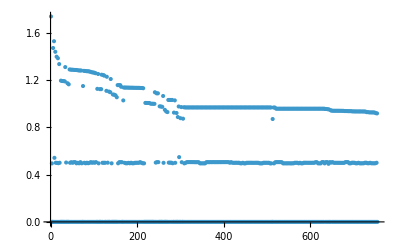

```mathematica
ListPlot[Table[Norm[Flatten[w,1][[i]]],{i,Length[v]}]]
```

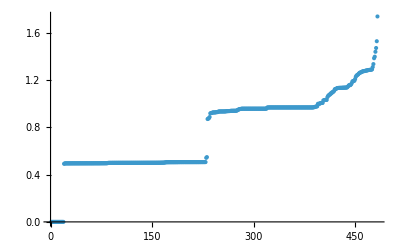

```mathematica
ListPlot[Union[Table[Norm[Flatten[w,1][[i]]],{i,Length[v]}]]]
```

```mathematica
Max[Union[Table[Norm[Flatten[w,1][[i]]],{i,Length[v]}]]]
```

1.73566

```mathematica
Apply[Plus,Union[Table[Norm[Flatten[w,1][[i]]],{i,Length[v]}]]]/Length[v]
```

0.485199

```mathematica
u=Table[If[Norm[w[[i]]]>1.25&&Norm[w[[i]]]<1.5,w[[i]],Nothing],{i,Length[v]}]
```

{{0,0,0.633731+1.32551 ⅈ},{0,1.39578+0.020717 ⅈ,0.498379-0.000941346 ⅈ},{0,1.38267+0.00995995 ⅈ,0.49315+0.051028 ⅈ},{0,-1.33297+0.028743 ⅈ,0.499699+0.00586373 ⅈ},{1.27489+0.292449 ⅈ,0,-0.501711-0.00143108 ⅈ},{0,1.28736+0.045338 ⅈ,0.499332-0.0052591 ⅈ},{0,1.28578+0.025013 ⅈ,0.50442-0.00343827 ⅈ},{0,-1.28578+0.0156267 ⅈ,0.499345+0.00597978 ⅈ},{0,-1.28479-0.00577213 ⅈ,0.504918-0.00349241 ⅈ},{0,-1.28307+0.04055 ⅈ,0.504784-0.0033128 ⅈ},{0,-1.28338+0.0238307 ⅈ,0.494875+0.00270813 ⅈ},{0,-1.28124-0.042725 ⅈ,0.499262+0.00597608 ⅈ},{0,1.27941-0.0235575 ⅈ,0.49514-0.00293266 ⅈ},{0,-1.27858+0.0417385 ⅈ,0.504788-0.00330754 ⅈ},{0,-1.27868-0.011004 ⅈ,0.495042-0.00274271 ⅈ},{0,-1.27514+0.0460161 ⅈ,0.499516-0.00588157 ⅈ},{0,-1.27488-0.0259885 ⅈ,0.495049-0.00272317 ⅈ},{0,1.27328-0.0144656 ⅈ,0.499772-0.00502152 ⅈ},{0,1.27239-0.0324751 ⅈ,0.495711-0.00266582 ⅈ},{0,-1.2713-0.0309675 ⅈ,0.499151-0.00514781 ⅈ},{0,-1.26808+0.00535858 ⅈ,0.504947-0.0035012 ⅈ},{0,1.26381-0.0388023 ⅈ,0.499403-0.00528466 ⅈ},{0,-1.25052+0.171974 ⅈ,0.503575-0.00362369 ⅈ},{0,1.26023-0.0352046 ⅈ,0.499706-0.00578793 ⅈ},{0,-1.25568-0.0354862 ⅈ,0.504976+0.00354605 ⅈ},{0,-1.24945-0.0229672 ⅈ,0.494813+0.00279086 ⅈ},{1.22292+0.226139 ⅈ,0,-0.499379+0.0057068 ⅈ},{0,1.23944-0.0409026 ⅈ,0.49933+0.00520444 ⅈ},{1.23578-0.00426893 ⅈ,0,-0.499362-0.0058305 ⅈ},{-1.21705-0.149544 ⅈ,0,-0.500269-0.0000646873 ⅈ},{-1.20588+0.0553131 ⅈ,0,-0.494873-0.00187312 ⅈ},{0,-1.14772+0.134735 ⅈ,0.495034+0.00251745 ⅈ},{0,1.14782+0.133556 ⅈ,0.505089+0.00355098 ⅈ},{0,1.14765-0.133785 ⅈ,0.503994-0.00403321 ⅈ}}

```mathematica
Re[u]
```

{{0,0,0.633731},{0,1.39578,0.498379},{0,1.38267,0.49315},{0,-1.33297,0.499699},{1.27489,0,-0.501711},{0,1.28736,0.499332},{0,1.28578,0.50442},{0,-1.28578,0.499345},{0,-1.28479,0.504918},{0,-1.28307,0.504784},{0,-1.28338,0.494875},{0,-1.28124,0.499262},{0,1.27941,0.49514},{0,-1.27858,0.504788},{0,-1.27868,0.495042},{0,-1.27514,0.499516},{0,-1.27488,0.495049},{0,1.27328,0.499772},{0,1.27239,0.495711},{0,-1.2713,0.499151},{0,-1.26808,0.504947},{0,1.26381,0.499403},{0,-1.25052,0.503575},{0,1.26023,0.499706},{0,-1.25568,0.504976},{0,-1.24945,0.494813},{1.22292,0,-0.499379},{0,1.23944,0.49933},{1.23578,0,-0.499362},{-1.21705,0,-0.500269},{-1.20588,0,-0.494873},{0,-1.14772,0.495034},{0,1.14782,0.505089},{0,1.14765,0.503994}}

```mathematica
t=Table[If[Norm[w[[i]]]>0.9&&Norm[w[[i]]]<1.1,w[[i]],Nothing],{i,Length[v]}]
```

{{0,0,0.235546-1.07022 ⅈ},{0,0,0.225487+1.05234 ⅈ},{0,0,0.262743+1.04233 ⅈ},{0,0,0.811126-0.697334 ⅈ},{0,0,0.307171+1.00729 ⅈ},{0,0,0.0216103-1.02612 ⅈ},{0,0,1.00525},{0,0,1.00488+8.52919×10^-9 ⅈ},{0,0,1.00473+4.99963×10^-9 ⅈ},{0,0,1.0047},{0,0,0.498689+0.865594 ⅈ},{0,0,0.500646-0.863638 ⅈ},{0,0,0.50218+0.862549 ⅈ},{0,0,0.499023-0.863533 ⅈ},{0,0,-0.0552511+0.974811 ⅈ},{0,0,-0.045963+0.973836 ⅈ},{-1.31381×10^-7+1.25189×10^-7 ⅈ,-2.78801×10^-8-2.22719×10^-7 ⅈ,0.0427201+0.971274 ⅈ},{0,0,0.111531+0.940279 ⅈ},{0,0,-0.0974668-0.928179 ⅈ},{7.7219×10^-8-3.28184×10^-8 ⅈ,-5.68436×10^-6+2.24269×10^-6 ⅈ,0.692278+0.617671 ⅈ},{6.33701×10^-8-4.88458×10^-8 ⅈ,-2.81311×10^-6+3.25377×10^-6 ⅈ,0.647725+0.65799 ⅈ},{-1.86948×10^-7+1.32601×10^-7 ⅈ,-1.86511×10^-7-1.64305×10^-7 ⅈ,0.0175348-0.919851 ⅈ},{0,0.854859-0.458191 ⅈ,0.504357+0.00342758 ⅈ},{0,-0.851219+0.462325 ⅈ,0.494432-0.00246933 ⅈ},{0,0.848426-0.464166 ⅈ,0.499131-0.00610711 ⅈ},{0,0.848315-0.463972 ⅈ,0.505087-0.00317239 ⅈ},{0,0.848311-0.463972 ⅈ,0.504902-0.00333198 ⅈ},{0,0.848312-0.463969 ⅈ,0.505062-0.00315039 ⅈ},{0,-0.848311+0.463969 ⅈ,0.504906-0.00319768 ⅈ},{0,-0.84831+0.463971 ⅈ,0.504912-0.00320213 ⅈ},{0,-0.848309+0.463971 ⅈ,0.50491-0.00320051 ⅈ},{0,-0.848309-0.46397 ⅈ,0.504336+0.00321417 ⅈ},{0,-0.848309+0.463968 ⅈ,0.504368-0.00317362 ⅈ},{0,0.848308-0.463968 ⅈ,0.504413-0.00307517 ⅈ},{0,0.848306-0.463971 ⅈ,0.504414-0.00307549 ⅈ},{0,-0.848304+0.463961 ⅈ,0.494622+0.00299686 ⅈ},{0,-0.848304+0.463961 ⅈ,0.494622+0.00299716 ⅈ},{0,0.848303+0.463961 ⅈ,0.494583-0.00315119 ⅈ},{0,-0.848304+0.46396 ⅈ,0.494574+0.00302534 ⅈ},{0,0.848302+0.463962 ⅈ,0.494775-0.00337041 ⅈ},{0,0.848302+0.46394 ⅈ,0.504521-0.00314777 ⅈ},{0,0.848303-0.463936 ⅈ,0.504875+0.00351447 ⅈ},{0,0.848299-0.463941 ⅈ,0.50415+0.00312562 ⅈ},{0,0.848301-0.463937 ⅈ,0.504875+0.00351419 ⅈ},{0,0.848299+0.46394 ⅈ,0.504515-0.00314364 ⅈ},{0,-0.8483+0.463939 ⅈ,0.504823+0.00333393 ⅈ},{0,0.8483-0.463937 ⅈ,0.504852+0.00349476 ⅈ},{0,0.848299-0.46394 ⅈ,0.50439+0.00340251 ⅈ},{0,0.848299-0.463939 ⅈ,0.504811+0.00345786 ⅈ},{0,0.848298+0.46394 ⅈ,0.504517-0.00314441 ⅈ},{0,0.848301-0.463935 ⅈ,0.504874+0.00351444 ⅈ},{0,0.8483+0.463937 ⅈ,0.504515-0.00314282 ⅈ},{0,0.8483-0.463935 ⅈ,0.504875+0.00351422 ⅈ},{0,0.8483-0.463935 ⅈ,0.50493+0.00370367 ⅈ},{0,0.848298-0.463936 ⅈ,0.504852+0.0034944 ⅈ},{0,-0.848299+0.463935 ⅈ,0.504813+0.00332689 ⅈ},{0,0.848298-0.463936 ⅈ,0.504872+0.00351173 ⅈ},{0,0.848298-0.463936 ⅈ,0.504873+0.00351375 ⅈ},{0,0.848287+0.463955 ⅈ,0.499642-0.00526099 ⅈ},{0,0.848298-0.463935 ⅈ,0.504874+0.00351312 ⅈ},{0,0.848286-0.463954 ⅈ,0.499699+0.00520918 ⅈ},{0,-0.848283-0.463959 ⅈ,0.499346-0.00583336 ⅈ},{0,-0.848285+0.463955 ⅈ,0.499487+0.00540969 ⅈ},{0,0.848284+0.463956 ⅈ,0.499859-0.00557769 ⅈ},{0,0.848282-0.463961 ⅈ,0.499233-0.00526591 ⅈ},{0,-0.848284+0.463956 ⅈ,0.4999+0.00526639 ⅈ},{0,0.84829-0.463944 ⅈ,0.495475-0.00270284 ⅈ},{0,-0.848291+0.463941 ⅈ,0.494409-0.00294621 ⅈ},{0,-0.84828-0.463963 ⅈ,0.499335+0.00532395 ⅈ},{0,-0.848292-0.463941 ⅈ,0.494627+0.00288724 ⅈ},{0,-0.848291+0.463941 ⅈ,0.494412-0.00294464 ⅈ},{0,-0.84828+0.463963 ⅈ,0.499303-0.00528799 ⅈ},{0,0.848279+0.463964 ⅈ,0.499322+0.00568668 ⅈ},{0,-0.84828+0.463962 ⅈ,0.499402-0.00537223 ⅈ},{0,0.848277-0.463967 ⅈ,0.499661-0.0063121 ⅈ},{0,-0.848278+0.463963 ⅈ,0.499474-0.00533701 ⅈ},{0,-0.848279+0.463962 ⅈ,0.499054-0.00526619 ⅈ},{0,-0.848282+0.463957 ⅈ,0.499379+0.00609684 ⅈ},{0,0.84828-0.46396 ⅈ,0.499506-0.00528898 ⅈ},{0,0.848282+0.463957 ⅈ,0.499557-0.00614035 ⅈ},{0,0.848282-0.463957 ⅈ,0.499259+0.00566801 ⅈ},{0,-0.84829-0.46394 ⅈ,0.494517+0.00294645 ⅈ},{0,-0.848291-0.463939 ⅈ,0.49463+0.0028857 ⅈ},{0,0.848291-0.463938 ⅈ,0.494672-0.00326044 ⅈ},{0,-0.848282-0.463954 ⅈ,0.499717-0.00594158 ⅈ},{0,-0.84828-0.463956 ⅈ,0.499394-0.0060066 ⅈ},{0,0.848275-0.463965 ⅈ,0.499555-0.00640309 ⅈ},{0,0.848279-0.463956 ⅈ,0.499166+0.00617702 ⅈ},{0,-0.84828-0.463955 ⅈ,0.499713-0.00596673 ⅈ},{0,0.848359-0.463694 ⅈ,0.494372-0.00285769 ⅈ},{0,0.848296-0.463709 ⅈ,0.494336-0.00287635 ⅈ},{0,-0.849239+0.461367 ⅈ,0.494337-0.0025114 ⅈ},{0,0.854533+0.450124 ⅈ,0.503996+0.00336167 ⅈ},{0,0.772275+0.564173 ⅈ,0.504874+0.00362256 ⅈ},{0,-0.772274-0.564173 ⅈ,0.504856+0.00350944 ⅈ},{0,0.772274-0.564172 ⅈ,0.504901-0.00350409 ⅈ},{0,0.772272+0.56417 ⅈ,0.504879+0.00362575 ⅈ},{0,-0.772269+0.564173 ⅈ,0.50438-0.00313888 ⅈ},{0,0.772268+0.564168 ⅈ,0.494652-0.00312025 ⅈ},{0,0.772267+0.564168 ⅈ,0.494649-0.00329933 ⅈ},{0,-0.772267-0.564169 ⅈ,0.494744-0.00316164 ⅈ},{0,-0.772267-0.564167 ⅈ,0.494744-0.00316076 ⅈ},{0,-0.772266-0.564168 ⅈ,0.494861-0.00301465 ⅈ},{0,-0.772266-0.564168 ⅈ,0.494862-0.00301432 ⅈ},{0,0.772267+0.564166 ⅈ,0.494438-0.00292456 ⅈ},{0,-0.772266-0.564168 ⅈ,0.494863-0.00301396 ⅈ},{0,-0.772265-0.564167 ⅈ,0.494772-0.00291135 ⅈ},{0,-0.772245-0.564194 ⅈ,0.499441-0.0060297 ⅈ},{0,0.772247-0.564191 ⅈ,0.499389+0.00542452 ⅈ},{0,-0.772243-0.564195 ⅈ,0.499612-0.00620446 ⅈ},{0,-0.772264-0.564167 ⅈ,0.494747-0.00252206 ⅈ},{0,0.772245-0.564191 ⅈ,0.49927+0.0053986 ⅈ},{0,-0.772264-0.564166 ⅈ,0.49476-0.00251584 ⅈ},{0,-0.772263-0.564166 ⅈ,0.494759-0.00251652 ⅈ},{0,0.772246+0.56419 ⅈ,0.499779-0.00542481 ⅈ},{0,-0.772246+0.56419 ⅈ,0.499474+0.00530845 ⅈ},{0,0.772244+0.564192 ⅈ,0.499615-0.00563987 ⅈ},{0,-0.77224-0.564197 ⅈ,0.499281+0.00597918 ⅈ},{0,0.772241+0.564194 ⅈ,0.499341+0.00526359 ⅈ},{0,0.772241+0.564194 ⅈ,0.499428+0.00526348 ⅈ},{0,-0.772239-0.564197 ⅈ,0.499179+0.00590026 ⅈ},{0,-0.772244+0.564189 ⅈ,0.499631+0.00524833 ⅈ},{0,-0.772241+0.564193 ⅈ,0.49934-0.00514953 ⅈ},{0,-0.772235-0.564163 ⅈ,0.50429-0.00297589 ⅈ},{0,0.772235+0.564162 ⅈ,0.504259-0.00301578 ⅈ},{0,-0.772231-0.564161 ⅈ,0.494652+0.00283238 ⅈ},{0,-0.77223+0.564161 ⅈ,0.49454-0.00272258 ⅈ},{0,0.772228-0.564162 ⅈ,0.494503-0.00312655 ⅈ},{0,-0.77223-0.564159 ⅈ,0.504988-0.0034268 ⅈ},{0,0.77223+0.564157 ⅈ,0.505286-0.00333459 ⅈ},{0,-0.772123-0.564241 ⅈ,0.494408+0.00268618 ⅈ},{0.939601-0.164905 ⅈ,0,-0.505143-0.00342318 ⅈ},{0.939583-0.164919 ⅈ,0,-0.505143-0.00342363 ⅈ},{0.763756-0.567969 ⅈ,0,-0.490765-0.00515081 ⅈ},{-0.934802+0.170873 ⅈ,0,-0.504981-0.00345515 ⅈ},{-6.30351×10^-8+3.21134×10^-7 ⅈ,0.89382+0.301409 ⅈ,0.487198+0.115775 ⅈ},{0.92289+0.17881 ⅈ,0,-0.505162-0.00386853 ⅈ},{0.921165-0.182189 ⅈ,0,-0.499439+0.00619018 ⅈ},{0.921133-0.182254 ⅈ,0,-0.499331+0.00624554 ⅈ},{-0.921124+0.18222 ⅈ,0,-0.499297+0.00614443 ⅈ},{-0.921071+0.182226 ⅈ,0,-0.499298+0.00615064 ⅈ},{0.920982+0.182183 ⅈ,0,-0.499215-0.00598716 ⅈ},{0.920959+0.18223 ⅈ,0,-0.499143-0.00600866 ⅈ},{-0.92079-0.182309 ⅈ,0,-0.498859-0.00596865 ⅈ},{-0.920656-0.18205 ⅈ,0,-0.498968-0.00537179 ⅈ},{-0.920586-0.181979 ⅈ,0,-0.498955-0.00540646 ⅈ},{0.919801-0.17551 ⅈ,0,-0.504871-0.00341915 ⅈ},{0.919757-0.175329 ⅈ,0,-0.505001-0.00368996 ⅈ},{-0.919587+0.175223 ⅈ,0,-0.504911-0.00398937 ⅈ},{-0.917633+0.182504 ⅈ,0,-0.494771+0.00285521 ⅈ},{0.917513+0.182428 ⅈ,0,-0.494697-0.0025431 ⅈ},{0.908794+0.221711 ⅈ,0,-0.499871+0.00371623 ⅈ},{-0.916818-0.17676 ⅈ,0,-0.499954+0.00521201 ⅈ},{0.916599-0.176898 ⅈ,0,-0.499541-0.00524246 ⅈ},{0.915721-0.179598 ⅈ,0,-0.494891-0.00304044 ⅈ},{-0.915582+0.179908 ⅈ,0,-0.495038-0.00253639 ⅈ},{0.916209+0.176393 ⅈ,0,-0.499592+0.00615071 ⅈ},{0.915537-0.179662 ⅈ,0,-0.494813-0.00308482 ⅈ},{0.915532-0.179667 ⅈ,0,-0.494813-0.00308621 ⅈ},{0.915532-0.179663 ⅈ,0,-0.494813-0.00308562 ⅈ},{-0.915243-0.179519 ⅈ,0,-0.495073+0.00345009 ⅈ},{0.915786+0.176453 ⅈ,0,-0.499736+0.00612005 ⅈ},{-0.915583-0.176401 ⅈ,0,-0.49995+0.0061996 ⅈ},{-0.89879-0.228385 ⅈ,0,-0.495385+0.00347234 ⅈ},{-0.898768-0.228402 ⅈ,0,-0.495388+0.00346921 ⅈ},{-0.909355+0.171343 ⅈ,0,-0.499357-0.00539217 ⅈ},{0.897593+0.223036 ⅈ,0,-0.495008+0.00325162 ⅈ},{0.897592+0.223037 ⅈ,0,-0.495007+0.00325128 ⅈ},{0.897458+0.22315 ⅈ,0,-0.495019+0.00324291 ⅈ},{0.897261+0.223318 ⅈ,0,-0.495038+0.00323381 ⅈ},{-0.897835-0.195429 ⅈ,0,-0.499497+0.00622871 ⅈ},{0.88934-0.222936 ⅈ,0,-0.499775-0.00361054 ⅈ},{0.889326-0.22294 ⅈ,0,-0.499758-0.00361961 ⅈ},{0.891162-0.189574 ⅈ,0,-0.499565-0.00622154 ⅈ},{0.891157-0.189573 ⅈ,0,-0.499565-0.00622153 ⅈ},{0.853907-0.238222 ⅈ,0,-0.499326-0.00201082 ⅈ},{0.845356+0.257353 ⅈ,0,-0.499772+0.00602879 ⅈ},{0.844591+0.259778 ⅈ,0,-0.500485+0.00176554 ⅈ},{-0.84051-0.262281 ⅈ,0,-0.500287+0.00155936 ⅈ},{-0.840839-0.249135 ⅈ,0,-0.501874+0.000797399 ⅈ},{-0.848432+0.214829 ⅈ,0,-0.495073-0.00272708 ⅈ},{-0.848424+0.214829 ⅈ,0,-0.495073-0.00272806 ⅈ},{0.837445+0.251221 ⅈ,0,-0.503277+0.00204623 ⅈ},{-0.837255-0.246816 ⅈ,0,-0.500017+0.00522049 ⅈ},{0.825426-0.257076 ⅈ,0,-0.499559-0.00620589 ⅈ},{-0.820825+0.255772 ⅈ,0,-0.50517-0.00363677 ⅈ},{-0.820825+0.255771 ⅈ,0,-0.50517-0.00363705 ⅈ},{-0.820824+0.255772 ⅈ,0,-0.50517-0.0036375 ⅈ},{-0.821256+0.25054 ⅈ,0,-0.499343-0.00543591 ⅈ},{0.808209+0.278518 ⅈ,0,-0.501091+0.00115674 ⅈ},{0.816056-0.251398 ⅈ,0,-0.504646-0.00319013 ⅈ},{0.816051-0.251397 ⅈ,0,-0.504645-0.00318792 ⅈ},{0.816029-0.251388 ⅈ,0,-0.504642-0.00318657 ⅈ},{0.816028-0.251389 ⅈ,0,-0.504641-0.00318695 ⅈ},{-0.81121+0.266343 ⅈ,0,-0.497878-0.00109207 ⅈ},{-0.815995+0.25104 ⅈ,0,-0.504523-0.00321712 ⅈ},{-0.815869+0.251 ⅈ,0,-0.504511-0.00320679 ⅈ},{0.814161-0.255904 ⅈ,0,-0.505237+0.00385156 ⅈ},{0.814034+0.25599 ⅈ,0,-0.505046-0.00385482 ⅈ},{-0.813612+0.255794 ⅈ,0,-0.49465-0.00294163 ⅈ},{0.813484-0.256109 ⅈ,0,-0.504392+0.00360032 ⅈ},{-0.813282-0.256183 ⅈ,0,-0.504159-0.00354821 ⅈ},{0.813293+0.256097 ⅈ,0,-0.504231-0.00345422 ⅈ},{0.813292+0.256096 ⅈ,0,-0.504231-0.00345362 ⅈ},{0.813294+0.25609 ⅈ,0,-0.504229-0.00344763 ⅈ},{0.813291+0.256096 ⅈ,0,-0.504232-0.00345261 ⅈ},{0.813292+0.256092 ⅈ,0,-0.504228-0.00344848 ⅈ},{0.813292+0.25609 ⅈ,0,-0.504226-0.00344716 ⅈ},{-0.811163+0.262614 ⅈ,0,-0.498957+0.00617995 ⅈ},{-0.811157+0.262613 ⅈ,0,-0.498956+0.00618 ⅈ},{0.810928+0.260082 ⅈ,0,-0.498988-0.00597306 ⅈ},{-0.810759-0.260292 ⅈ,0,-0.498665-0.00607398 ⅈ},{0.810606+0.259831 ⅈ,0,-0.498851-0.00545363 ⅈ},{0.80992-0.259573 ⅈ,0,-0.499196+0.00548164 ⅈ},{-0.803238-0.276603 ⅈ,0,-0.499199+0.00197525 ⅈ},{-0.806609-0.266334 ⅈ,0,-0.501208+0.00088016 ⅈ},{0.81082+0.251488 ⅈ,0,-0.504398+0.0033205 ⅈ},{-0.810392-0.251507 ⅈ,0,-0.504341+0.00328846 ⅈ},{-0.810385-0.251517 ⅈ,0,-0.504326+0.00328339 ⅈ},{0.81042+0.251375 ⅈ,0,-0.504461+0.00340629 ⅈ},{0.810413+0.251388 ⅈ,0,-0.504444+0.00339706 ⅈ},{-0.806791+0.259652 ⅈ,0,-0.495079+0.00253735 ⅈ},{0.806339+0.259776 ⅈ,0,-0.494428-0.002457 ⅈ},{0.806248+0.259919 ⅈ,0,-0.494237-0.00254316 ⅈ},{-0.806139-0.259446 ⅈ,0,-0.494453-0.00198556 ⅈ},{0.808352-0.251342 ⅈ,0,-0.502351-0.00485528 ⅈ},{0.801698+0.270881 ⅈ,0,-0.497584+0.00168123 ⅈ},{-0.808234-0.245276 ⅈ,0,-0.49527+0.00356663 ⅈ},{0.804136-0.256511 ⅈ,0,-0.494436-0.0024493 ⅈ},{-0.807524-0.243627 ⅈ,0,-0.49506+0.00373505 ⅈ},{-0.8074-0.243314 ⅈ,0,-0.495026+0.00376187 ⅈ},{0.803548+0.253805 ⅈ,0,-0.504309-0.00353403 ⅈ},{0.804462+0.246929 ⅈ,0,-0.494868+0.00328615 ⅈ},{0.792782+0.275698 ⅈ,0,-0.504729-0.00394132 ⅈ},{-0.789616+0.268559 ⅈ,0,-0.498766-0.00110885 ⅈ},{0,0.54492+0.62842 ⅈ,0.499644-0.00642781 ⅈ},{0,0.544922-0.628417 ⅈ,0.499352+0.00574369 ⅈ},{0,-0.544921+0.628415 ⅈ,0.49962+0.00560163 ⅈ},{0,-0.544938+0.6284 ⅈ,0.504459-0.00338368 ⅈ},{0,0.544937-0.6284 ⅈ,0.504406-0.00323337 ⅈ},{0,0.544942+0.628395 ⅈ,0.494486-0.00326016 ⅈ},{0,-0.544936-0.6284 ⅈ,0.50422+0.00322979 ⅈ},{0,0.544936+0.6284 ⅈ,0.504251+0.0031563 ⅈ},{0,-0.544918+0.628414 ⅈ,0.499774-0.00553872 ⅈ},{0,-0.544913-0.628416 ⅈ,0.49914+0.00604389 ⅈ},{0,0.544916+0.628413 ⅈ,0.499365+0.00537191 ⅈ},{0,-0.544915+0.628413 ⅈ,0.499281-0.00547091 ⅈ},{0,-0.54492-0.628381 ⅈ,0.506214-0.00117526 ⅈ},{0,-0.544912-0.628387 ⅈ,0.494728+0.00262911 ⅈ},{0,-0.544912-0.628387 ⅈ,0.494728+0.0026298 ⅈ},{0,-0.544912-0.628387 ⅈ,0.494728+0.00262948 ⅈ},{0,0.544909-0.628385 ⅈ,0.494415-0.0031249 ⅈ},{-0.795173-0.241259 ⅈ,0,-0.504997+0.00303441 ⅈ},{0.798418-0.205567 ⅈ,0,-0.504881+0.00377659 ⅈ},{0.798318-0.205315 ⅈ,0,-0.504881+0.0037767 ⅈ},{0.78546+0.246398 ⅈ,0,-0.505102+0.0031474 ⅈ},{-0.775992-0.26735 ⅈ,0,-0.50124-0.00184034 ⅈ},{-0.774478-0.269719 ⅈ,0,-0.49813-0.00293566 ⅈ},{-0.775553-0.265193 ⅈ,0,-0.50239+0.000465972 ⅈ},{0.781038+0.24727 ⅈ,0,-0.499804+0.00547502 ⅈ},{-0.773176-0.267855 ⅈ,0,-0.498391-4.65731×10^-6 ⅈ},{0,0.502144-0.645986 ⅈ,0.499405+0.00229288 ⅈ},{-0.777658-0.254009 ⅈ,0,-0.50015+0.00577823 ⅈ},{-0.773276-0.267001 ⅈ,0,-0.498983+0.000458956 ⅈ},{0.775816-0.256424 ⅈ,0,-0.50409+0.00319917 ⅈ},{-0.77194-0.267166 ⅈ,0,-0.497621+0.00127325 ⅈ},{-0.771262-0.266965 ⅈ,0,-0.497249+0.00218417 ⅈ},{-0.771958+0.261879 ⅈ,0,-0.498018+0.000922011 ⅈ},{-0.77176+0.261951 ⅈ,0,-0.497783+0.000811886 ⅈ},{-0.771715+0.261566 ⅈ,0,-0.497998+0.000963431 ⅈ},{-0.769603-0.261412 ⅈ,0,-0.495031+0.00392256 ⅈ},{-0.772691-0.252063 ⅈ,0,-0.495523+0.00351418 ⅈ},{0.770225+0.257624 ⅈ,0,-0.494896+0.00338136 ⅈ},{0.770662+0.256027 ⅈ,0,-0.49499+0.00332053 ⅈ},{0.766584-0.267747 ⅈ,0,-0.501918+0.0016728 ⅈ},{0.766491-0.267682 ⅈ,0,-0.501908+0.00156195 ⅈ},{0.766377-0.267655 ⅈ,0,-0.501825+0.00145714 ⅈ},{0.769123+0.259359 ⅈ,0,-0.500756+0.00233966 ⅈ},{0,0.484163-0.650699 ⅈ,0.498273-0.00159528 ⅈ},{0.784948+0.203889 ⅈ,0,-0.494464-0.00239214 ⅈ},{0,-0.498687+0.638365 ⅈ,0.498673+0.00560269 ⅈ},{-0.766395+0.253945 ⅈ,0,-0.497714+0.000943637 ⅈ},{0,0.494816-0.630185 ⅈ,0.499505+0.00555887 ⅈ},{0,0.494816+0.62629 ⅈ,0.499687-0.0065067 ⅈ},{0,-0.494816-0.626288 ⅈ,0.499602-0.00622702 ⅈ},{0,-0.494816+0.626288 ⅈ,0.499673+0.00620529 ⅈ},{0,0.494818-0.626284 ⅈ,0.499417+0.00545429 ⅈ},{0,0.494811-0.626287 ⅈ,0.499476-0.00605731 ⅈ},{0,-0.494831+0.626268 ⅈ,0.504432-0.00336965 ⅈ},{0,-0.494831+0.626268 ⅈ,0.504432-0.00336919 ⅈ},{0,-0.494831+0.626268 ⅈ,0.504432-0.00336942 ⅈ},{0,-0.494831+0.626268 ⅈ,0.504396-0.00333341 ⅈ},{0,-0.494831+0.626268 ⅈ,0.504394-0.00333128 ⅈ},{0,-0.494831+0.626268 ⅈ,0.504361-0.00329913 ⅈ},{0,-0.494811+0.626283 ⅈ,0.499323-0.00541299 ⅈ},{0,0.494811+0.626283 ⅈ,0.499321+0.00541468 ⅈ},{0,0.49483-0.626268 ⅈ,0.504359-0.00318528 ⅈ},{0,-0.494835+0.626264 ⅈ,0.494505+0.00334012 ⅈ},{0,0.494835+0.626264 ⅈ,0.494524-0.0032928 ⅈ},{0,-0.49481-0.626283 ⅈ,0.499095+0.00554294 ⅈ},{0,-0.494802-0.626261 ⅈ,0.50502-0.00327521 ⅈ},{0,-0.494802-0.626261 ⅈ,0.505019-0.00327457 ⅈ},{0,-0.494802-0.626261 ⅈ,0.505021-0.0032755 ⅈ},{0,-0.494802+0.626261 ⅈ,0.50507+0.00329821 ⅈ},{0,0.494802+0.62626 ⅈ,0.505174-0.0033225 ⅈ},{0,0.494802+0.62626 ⅈ,0.505177-0.00332568 ⅈ},{0,0.494802+0.62626 ⅈ,0.505177-0.00332495 ⅈ},{0,0.494802-0.626258 ⅈ,0.494522-0.00312264 ⅈ},{0,0.491615-0.628299 ⅈ,0.498941-0.00602329 ⅈ},{-0.752478-0.263109 ⅈ,0,-0.497096-0.000937931 ⅈ},{-0.752312-0.262893 ⅈ,0,-0.497116-0.000893255 ⅈ},{-0.761538+0.229202 ⅈ,0,-0.498974+0.00528303 ⅈ},{0.754632-0.250998 ⅈ,0,-0.501267-0.00128321 ⅈ},{0,-0.491481+0.622939 ⅈ,0.505036-0.00389413 ⅈ},{0.759043-0.229837 ⅈ,0,-0.499126+0.00540966 ⅈ},{0,-0.497279+0.617552 ⅈ,0.49974+0.00651841 ⅈ},{0,-0.49725+0.617527 ⅈ,0.499743+0.00650307 ⅈ},{0.758852-0.229439 ⅈ,0,-0.499103+0.00550186 ⅈ},{0,0.497491-0.616827 ⅈ,0.499468+0.00644395 ⅈ},{0,-0.471842+0.636141 ⅈ,0.499898-0.00188806 ⅈ},{0,0.501523-0.612342 ⅈ,0.495153-0.00253866 ⅈ},{0,0.46977-0.636178 ⅈ,0.499792-0.0019371 ⅈ},{-0.754191-0.230424 ⅈ,0,-0.494817-0.00169289 ⅈ},{0,0.495146-0.613259 ⅈ,0.499285-0.00551618 ⅈ},{0,0.495145-0.61326 ⅈ,0.499286-0.00551462 ⅈ},{0,-0.495448+0.612682 ⅈ,0.499064-0.00590069 ⅈ},{0.751534+0.230327 ⅈ,0,-0.504264-0.00371814 ⅈ},{-0.749972+0.234544 ⅈ,0,-0.504868+0.00389968 ⅈ},{-0.747758+0.240943 ⅈ,0,-0.50523-0.00356969 ⅈ},{0.749463-0.234542 ⅈ,0,-0.505063+0.00399373 ⅈ},{0.749464-0.234539 ⅈ,0,-0.505063+0.00399251 ⅈ},{0.749529-0.234312 ⅈ,0,-0.505033+0.00396254 ⅈ},{0.749606-0.234014 ⅈ,0,-0.504994+0.00392381 ⅈ},{-0.750851-0.229849 ⅈ,0,-0.504213-0.00382742 ⅈ},{-0.750813-0.229872 ⅈ,0,-0.504216-0.00383184 ⅈ},{0.750681-0.227439 ⅈ,0,-0.504534-0.00296203 ⅈ},{0.750678-0.227448 ⅈ,0,-0.504532-0.0029642 ⅈ},{0.750683-0.227392 ⅈ,0,-0.50453-0.00296085 ⅈ},{0.750683-0.227392 ⅈ,0,-0.50453-0.00296078 ⅈ},{0.750684-0.227374 ⅈ,0,-0.504529-0.00295866 ⅈ},{0.749534+0.225119 ⅈ,0,-0.498868-0.0052729 ⅈ},{-0.750197-0.219999 ⅈ,0,-0.498624-0.00528441 ⅈ},{-0.7498-0.219949 ⅈ,0,-0.498617-0.0053025 ⅈ},{-0.739667+0.24409 ⅈ,0,-0.498917-0.000621368 ⅈ},{0.73889-0.24527 ⅈ,0,-0.4997-0.00623444 ⅈ},{-0.737122+0.248042 ⅈ,0,-0.499431-0.00609817 ⅈ},{0.733594-0.257733 ⅈ,0,-0.499285+0.00438178 ⅈ},{-0.736147+0.249856 ⅈ,0,-0.499404-0.00622214 ⅈ},{0.735725+0.250575 ⅈ,0,-0.49847-0.00165206 ⅈ},{-0.738311+0.239949 ⅈ,0,-0.50059-0.00185194 ⅈ},{0,-0.477387+0.610598 ⅈ,0.494208-0.00274086 ⅈ},{0,-0.477387+0.610597 ⅈ,0.494208-0.00274089 ⅈ},{-0.739929+0.223693 ⅈ,0,-0.494612+0.00288327 ⅈ},{-0.732972+0.244465 ⅈ,0,-0.499694+0.00209611 ⅈ},{-0.731231-0.248128 ⅈ,0,-0.496365-0.00135156 ⅈ},{-0.729736+0.249234 ⅈ,0,-0.495156-0.00286007 ⅈ},{0.72986-0.247839 ⅈ,0,-0.494869-0.00320672 ⅈ},{0.735626+0.229221 ⅈ,0,-0.49899+0.00649105 ⅈ},{0.73776+0.221322 ⅈ,0,-0.494005+0.000961112 ⅈ},{-0.729954+0.245727 ⅈ,0,-0.49567+0.00198935 ⅈ},{-0.73116+0.24143 ⅈ,0,-0.499214+0.00369668 ⅈ},{0.724611-0.241238 ⅈ,0,-0.499474+0.0022608 ⅈ},{0.722799+0.240916 ⅈ,0,-0.498891-0.00454015 ⅈ},{0.716106+0.247328 ⅈ,0,-0.499036-0.00159485 ⅈ},{-0.714115-0.241935 ⅈ,0,-0.49916-0.0016988 ⅈ},{0.718129+0.223367 ⅈ,0,-0.504187-0.000710539 ⅈ},{-0.715052-0.231491 ⅈ,0,-0.501346+0.00158493 ⅈ}}

```mathematica
Re[t]
```

{{0,0,0.235546},{0,0,0.225487},{0,0,0.262743},{0,0,0.811126},{0,0,0.307171},{0,0,0.0216103},{0,0,1.00525},{0,0,1.00488},{0,0,1.00473},{0,0,1.0047},{0,0,0.498689},{0,0,0.500646},{0,0,0.50218},{0,0,0.499023},{0,0,-0.0552511},{0,0,-0.045963},{-1.31381×10^-7,-2.78801×10^-8,0.0427201},{0,0,0.111531},{0,0,-0.0974668},{7.7219×10^-8,-5.68436×10^-6,0.692278},{6.33701×10^-8,-2.81311×10^-6,0.647725},{-1.86948×10^-7,-1.86511×10^-7,0.0175348},{0,0.854859,0.504357},{0,-0.851219,0.494432},{0,0.848426,0.499131},{0,0.848315,0.505087},{0,0.848311,0.504902},{0,0.848312,0.505062},{0,-0.848311,0.504906},{0,-0.84831,0.504912},{0,-0.848309,0.50491},{0,-0.848309,0.504336},{0,-0.848309,0.504368},{0,0.848308,0.504413},{0,0.848306,0.504414},{0,-0.848304,0.494622},{0,-0.848304,0.494622},{0,0.848303,0.494583},{0,-0.848304,0.494574},{0,0.848302,0.494775},{0,0.848302,0.504521},{0,0.848303,0.504875},{0,0.848299,0.50415},{0,0.848301,0.504875},{0,0.848299,0.504515},{0,-0.8483,0.504823},{0,0.8483,0.504852},{0,0.848299,0.50439},{0,0.848299,0.504811},{0,0.848298,0.504517},{0,0.848301,0.504874},{0,0.8483,0.504515},{0,0.8483,0.504875},{0,0.8483,0.50493},{0,0.848298,0.504852},{0,-0.848299,0.504813},{0,0.848298,0.504872},{0,0.848298,0.504873},{0,0.848287,0.499642},{0,0.848298,0.504874},{0,0.848286,0.499699},{0,-0.848283,0.499346},{0,-0.848285,0.499487},{0,0.848284,0.499859},{0,0.848282,0.499233},{0,-0.848284,0.4999},{0,0.84829,0.495475},{0,-0.848291,0.494409},{0,-0.84828,0.499335},{0,-0.848292,0.494627},{0,-0.848291,0.494412},{0,-0.84828,0.499303},{0,0.848279,0.499322},{0,-0.84828,0.499402},{0,0.848277,0.499661},{0,-0.848278,0.499474},{0,-0.848279,0.499054},{0,-0.848282,0.499379},{0,0.84828,0.499506},{0,0.848282,0.499557},{0,0.848282,0.499259},{0,-0.84829,0.494517},{0,-0.848291,0.49463},{0,0.848291,0.494672},{0,-0.848282,0.499717},{0,-0.84828,0.499394},{0,0.848275,0.499555},{0,0.848279,0.499166},{0,-0.84828,0.499713},{0,0.848359,0.494372},{0,0.848296,0.494336},{0,-0.849239,0.494337},{0,0.854533,0.503996},{0,0.772275,0.504874},{0,-0.772274,0.504856},{0,0.772274,0.504901},{0,0.772272,0.504879},{0,-0.772269,0.50438},{0,0.772268,0.494652},{0,0.772267,0.494649},{0,-0.772267,0.494744},{0,-0.772267,0.494744},{0,-0.772266,0.494861},{0,-0.772266,0.494862},{0,0.772267,0.494438},{0,-0.772266,0.494863},{0,-0.772265,0.494772},{0,-0.772245,0.499441},{0,0.772247,0.499389},{0,-0.772243,0.499612},{0,-0.772264,0.494747},{0,0.772245,0.49927},{0,-0.772264,0.49476},{0,-0.772263,0.494759},{0,0.772246,0.499779},{0,-0.772246,0.499474},{0,0.772244,0.499615},{0,-0.77224,0.499281},{0,0.772241,0.499341},{0,0.772241,0.499428},{0,-0.772239,0.499179},{0,-0.772244,0.499631},{0,-0.772241,0.49934},{0,-0.772235,0.50429},{0,0.772235,0.504259},{0,-0.772231,0.494652},{0,-0.77223,0.49454},{0,0.772228,0.494503},{0,-0.77223,0.504988},{0,0.77223,0.505286},{0,-0.772123,0.494408},{0.939601,0,-0.505143},{0.939583,0,-0.505143},{0.763756,0,-0.490765},{-0.934802,0,-0.504981},{-6.30351×10^-8,0.89382,0.487198},{0.92289,0,-0.505162},{0.921165,0,-0.499439},{0.921133,0,-0.499331},{-0.921124,0,-0.499297},{-0.921071,0,-0.499298},{0.920982,0,-0.499215},{0.920959,0,-0.499143},{-0.92079,0,-0.498859},{-0.920656,0,-0.498968},{-0.920586,0,-0.498955},{0.919801,0,-0.504871},{0.919757,0,-0.505001},{-0.919587,0,-0.504911},{-0.917633,0,-0.494771},{0.917513,0,-0.494697},{0.908794,0,-0.499871},{-0.916818,0,-0.499954},{0.916599,0,-0.499541},{0.915721,0,-0.494891},{-0.915582,0,-0.495038},{0.916209,0,-0.499592},{0.915537,0,-0.494813},{0.915532,0,-0.494813},{0.915532,0,-0.494813},{-0.915243,0,-0.495073},{0.915786,0,-0.499736},{-0.915583,0,-0.49995},{-0.89879,0,-0.495385},{-0.898768,0,-0.495388},{-0.909355,0,-0.499357},{0.897593,0,-0.495008},{0.897592,0,-0.495007},{0.897458,0,-0.495019},{0.897261,0,-0.495038},{-0.897835,0,-0.499497},{0.88934,0,-0.499775},{0.889326,0,-0.499758},{0.891162,0,-0.499565},{0.891157,0,-0.499565},{0.853907,0,-0.499326},{0.845356,0,-0.499772},{0.844591,0,-0.500485},{-0.84051,0,-0.500287},{-0.840839,0,-0.501874},{-0.848432,0,-0.495073},{-0.848424,0,-0.495073},{0.837445,0,-0.503277},{-0.837255,0,-0.500017},{0.825426,0,-0.499559},{-0.820825,0,-0.50517},{-0.820825,0,-0.50517},{-0.820824,0,-0.50517},{-0.821256,0,-0.499343},{0.808209,0,-0.501091},{0.816056,0,-0.504646},{0.816051,0,-0.504645},{0.816029,0,-0.504642},{0.816028,0,-0.504641},{-0.81121,0,-0.497878},{-0.815995,0,-0.504523},{-0.815869,0,-0.504511},{0.814161,0,-0.505237},{0.814034,0,-0.505046},{-0.813612,0,-0.49465},{0.813484,0,-0.504392},{-0.813282,0,-0.504159},{0.813293,0,-0.504231},{0.813292,0,-0.504231},{0.813294,0,-0.504229},{0.813291,0,-0.504232},{0.813292,0,-0.504228},{0.813292,0,-0.504226},{-0.811163,0,-0.498957},{-0.811157,0,-0.498956},{0.810928,0,-0.498988},{-0.810759,0,-0.498665},{0.810606,0,-0.498851},{0.80992,0,-0.499196},{-0.803238,0,-0.499199},{-0.806609,0,-0.501208},{0.81082,0,-0.504398},{-0.810392,0,-0.504341},{-0.810385,0,-0.504326},{0.81042,0,-0.504461},{0.810413,0,-0.504444},{-0.806791,0,-0.495079},{0.806339,0,-0.494428},{0.806248,0,-0.494237},{-0.806139,0,-0.494453},{0.808352,0,-0.502351},{0.801698,0,-0.497584},{-0.808234,0,-0.49527},{0.804136,0,-0.494436},{-0.807524,0,-0.49506},{-0.8074,0,-0.495026},{0.803548,0,-0.504309},{0.804462,0,-0.494868},{0.792782,0,-0.504729},{-0.789616,0,-0.498766},{0,0.54492,0.499644},{0,0.544922,0.499352},{0,-0.544921,0.49962},{0,-0.544938,0.504459},{0,0.544937,0.504406},{0,0.544942,0.494486},{0,-0.544936,0.50422},{0,0.544936,0.504251},{0,-0.544918,0.499774},{0,-0.544913,0.49914},{0,0.544916,0.499365},{0,-0.544915,0.499281},{0,-0.54492,0.506214},{0,-0.544912,0.494728},{0,-0.544912,0.494728},{0,-0.544912,0.494728},{0,0.544909,0.494415},{-0.795173,0,-0.504997},{0.798418,0,-0.504881},{0.798318,0,-0.504881},{0.78546,0,-0.505102},{-0.775992,0,-0.50124},{-0.774478,0,-0.49813},{-0.775553,0,-0.50239},{0.781038,0,-0.499804},{-0.773176,0,-0.498391},{0,0.502144,0.499405},{-0.777658,0,-0.50015},{-0.773276,0,-0.498983},{0.775816,0,-0.50409},{-0.77194,0,-0.497621},{-0.771262,0,-0.497249},{-0.771958,0,-0.498018},{-0.77176,0,-0.497783},{-0.771715,0,-0.497998},{-0.769603,0,-0.495031},{-0.772691,0,-0.495523},{0.770225,0,-0.494896},{0.770662,0,-0.49499},{0.766584,0,-0.501918},{0.766491,0,-0.501908},{0.766377,0,-0.501825},{0.769123,0,-0.500756},{0,0.484163,0.498273},{0.784948,0,-0.494464},{0,-0.498687,0.498673},{-0.766395,0,-0.497714},{0,0.494816,0.499505},{0,0.494816,0.499687},{0,-0.494816,0.499602},{0,-0.494816,0.499673},{0,0.494818,0.499417},{0,0.494811,0.499476},{0,-0.494831,0.504432},{0,-0.494831,0.504432},{0,-0.494831,0.504432},{0,-0.494831,0.504396},{0,-0.494831,0.504394},{0,-0.494831,0.504361},{0,-0.494811,0.499323},{0,0.494811,0.499321},{0,0.49483,0.504359},{0,-0.494835,0.494505},{0,0.494835,0.494524},{0,-0.49481,0.499095},{0,-0.494802,0.50502},{0,-0.494802,0.505019},{0,-0.494802,0.505021},{0,-0.494802,0.50507},{0,0.494802,0.505174},{0,0.494802,0.505177},{0,0.494802,0.505177},{0,0.494802,0.494522},{0,0.491615,0.498941},{-0.752478,0,-0.497096},{-0.752312,0,-0.497116},{-0.761538,0,-0.498974},{0.754632,0,-0.501267},{0,-0.491481,0.505036},{0.759043,0,-0.499126},{0,-0.497279,0.49974},{0,-0.49725,0.499743},{0.758852,0,-0.499103},{0,0.497491,0.499468},{0,-0.471842,0.499898},{0,0.501523,0.495153},{0,0.46977,0.499792},{-0.754191,0,-0.494817},{0,0.495146,0.499285},{0,0.495145,0.499286},{0,-0.495448,0.499064},{0.751534,0,-0.504264},{-0.749972,0,-0.504868},{-0.747758,0,-0.50523},{0.749463,0,-0.505063},{0.749464,0,-0.505063},{0.749529,0,-0.505033},{0.749606,0,-0.504994},{-0.750851,0,-0.504213},{-0.750813,0,-0.504216},{0.750681,0,-0.504534},{0.750678,0,-0.504532},{0.750683,0,-0.50453},{0.750683,0,-0.50453},{0.750684,0,-0.504529},{0.749534,0,-0.498868},{-0.750197,0,-0.498624},{-0.7498,0,-0.498617},{-0.739667,0,-0.498917},{0.73889,0,-0.4997},{-0.737122,0,-0.499431},{0.733594,0,-0.499285},{-0.736147,0,-0.499404},{0.735725,0,-0.49847},{-0.738311,0,-0.50059},{0,-0.477387,0.494208},{0,-0.477387,0.494208},{-0.739929,0,-0.494612},{-0.732972,0,-0.499694},{-0.731231,0,-0.496365},{-0.729736,0,-0.495156},{0.72986,0,-0.494869},{0.735626,0,-0.49899},{0.73776,0,-0.494005},{-0.729954,0,-0.49567},{-0.73116,0,-0.499214},{0.724611,0,-0.499474},{0.722799,0,-0.498891},{0.716106,0,-0.499036},{-0.714115,0,-0.49916},{0.718129,0,-0.504187},{-0.715052,0,-0.501346}}

```mathematica
(*end*)
```

```mathematica
(*Mathematica*)
```

```mathematica
(* Mandelbulb type program for a ListSurfacePlot3D double program written using Paul Nylander's base program and voxels idea*)
ClearAll[x,y,z]
n=500;m0=3;norm[x_]:=x.x;pc0={0,0.6176710261974764,0.692277537822295};
BagulaSquare[{x_, y_, z_}] := Module[{rxz2=x^2+z^2},If[rxz2==0,{0,0,0},{2*x*z,-2*y*z,x^2+y^2-z^2}]];
Mandelbrot3D[pc_]:=Module[{p=pc,i=0},While[i<24&&norm[p]<4,p=BagulaSquare[p]+pc0;i++];i];
```

```mathematica
image1=Flatten[ParallelTable[z=1.5;While[z≥0.0 &&Mandelbrot3D[{x,y,z}]<24&&Abs[z]>1.0824674490095276*^-15,z-=m0/n];{x,y,z},{y,-1.5,1.5,m0/n},{x,-2,1,m0/n}],1];
```

```mathematica
(*ListDensityPlot3D[image1,ViewPoint->Above];*)
```

```mathematica
Dimensions[image1]
```

{251001,3}

```mathematica
min1=Min[ParallelTable[Norm[image1[[i,3]]],{i,Length[image1]}]]
```

1.26114×10^-15

```mathematica
image11=ParallelTable[If[Norm[image1[[i,3]]]>min1,image1[[i]],Nothing],{i,Length[image1]}];
```

```mathematica
Dimensions[image11]
```

{8137,3}

```mathematica
(*ListPointPlot3D[image11,ColorFunction->"Rainbow",PlotStyle->PointSize[0.002],ImageSize->{2000,2000}]*)
```

```mathematica
image2=Flatten[ParallelTable[z=-1.5;While[z≤0.0&&Mandelbrot3D[{x,y,z}]<24&&Abs[z]>0,z+=m0/n];{x,y,z},{y,-1.5,1.5,m0/n},{x,-2,1,m0/n}],1];
```

```mathematica
Dimensions[image2]
```

{251001,3}

```mathematica
min2=Min[Table[Norm[image2[[i,3]]],{i,Length[image2]}]]
```

1.26114×10^-15

```mathematica
image21=ParallelTable[If[Norm[image2[[i,3]]]>min2,image2[[i]],Nothing],{i,Length[image2]}];
```

```mathematica
Dimensions[image21]
```

{8137,3}

```mathematica
image3=Flatten[ParallelTable[y=1.5;While[y≥0. &&Mandelbrot3D[{x,y,z}]<24&&Abs[y]>0,y-=m0/n];{x,y,z},{z,-1.5,1.5,m0/n},{x,-2,1,m0/n}],1];
```

```mathematica
min3=Min[ParallelTable[Norm[image3[[i,2]]],{i,Length[image3]}]]
```

1.26114×10^-15

```mathematica
image31=ParallelTable[If[Norm[image3[[i,2]]]>min3,image3[[i]],Nothing],{i,Length[image3]}];
```

```mathematica
image4=Flatten[ParallelTable[y=-1.5;While[y≤0&&Mandelbrot3D[{x,y,z}]<24&&Abs[y]>0,y+=m0/n];{x,y,z},{z,-1.5,1.5,m0/n},{x,-2,1,m0/n}],1];
```

```mathematica
min4=Min[ParallelTable[Norm[image4[[i,2]]],{i,Length[image4]}]]
```

1.26114×10^-15

```mathematica
image41=ParallelTable[If[Norm[image4[[i,2]]]>min4,image4[[i]],Nothing],{i,Length[image4]}];
```

```mathematica
image5=Delete[Reverse[Union[Flatten[ParallelTable[x=1.5;While[x≥0 &&Mandelbrot3D[{x,y,z}]<24&&Abs[x]>0,x-=m0/n];{x,y,z},{y,-1.5,1.5,m0/n},{z,-2,1,m0/n}],1]]],1];
```

```mathematica
Dimensions[image5]
```

{251000,3}

```mathematica
min5=Min[ParallelTable[Norm[image5[[i,1]]],{i,Length[image5]}]]
```

1.26114×10^-15

```mathematica
image51=ParallelTable[If[Norm[image5[[i,1]]]<=min5,Nothing,image5[[i]]],{i,Length[image5]}];
```

```mathematica
Dimensions[image51]
```

{6645,3}

```mathematica
image6=Flatten[ParallelTable[x=-2;While[x≤0&&Mandelbrot3D[{x,y,z}]<24&&Abs[x]>0,x+=m0/n];{x,y,z},{y,-1.5,1.5,m0/n},{z,-1.5,1.5,m0/n}],1];
```

```mathematica
Dimensions[image6]
```

{251001,3}

```mathematica
min6=2*Min[ParallelTable[Norm[image6[[i,1]]],{i,Length[image6]}]]
```

1/250

```mathematica
image61=ParallelTable[If[Norm[image6[[i,1]]]<=min6,Nothing,image6[[i]]],{i,Length[image6]}];
```

```mathematica
Dimensions[image61]
```

{7080,3}

```mathematica
(*g1=ListPointPlot3D[Join[image11,image21],Axes->False,Boxed->False]
g2=ListPointPlot3D[image21,Axes->False,Boxed->False]
ga=Show[{g1,g2},PlotRange->All]
g3=ListPointPlot3D[image31,Axes->False,Boxed->False]
g4=ListPointPlot3D[image41,Axes->False,Boxed->False]
gb=Show[{g1,g3},PlotRange->All,ViewPoint->Above]*)
```

```mathematica
g5=ListPointPlot3D[image51,Axes->False,Boxed->False];
g6=ListPointPlot3D[image61,Axes->False,Boxed->False];
```

```mathematica
(*gc=Show[{g5,g6},PlotRange->All]*)
(*Export["Mandelbulb3d100.stl",g]*)
```

```mathematica
w=Join[image11,image21,image31,image41,image51,image61];
```

```mathematica
Length[w]
```

47509

```mathematica
Dimensions[w]
```

{47509,3}

```mathematica
g1=ListPointPlot3D[w,ColorFunction->"Rainbow",PlotStyle->PointSize[0.002],ImageSize->{2000,2000}];
```

```mathematica
Export["Julia_2truePC6_Quadratic3d_U1SO2_Nylander2_500_g1.jpg",g1]
```

Julia_2truePC6_Quadratic3d_U1SO2_Nylander2_500_g1.jpg

```mathematica
g2=Show[g1,ViewPoint->Bottom,ImageSize->{2000,2000}];
g3=Show[g1,ViewPoint->{2,2,2},ImageSize->{2000,2000}];
g4=Show[g1,ViewPoint->{-2,0,0},ImageSize->{2000,2000}];
```

```mathematica
Export["Julia_2truePC6_Quadratic3d_U1SO2_Nylander2_500_g4.jpg",g4]
```

Julia_2truePC6_Quadratic3d_U1SO2_Nylander2_500_g4.jpg

```mathematica
Export["Julia_2truePC6_Quadratic3d_U1SO2_Nylander2_500_grid.jpg",Rasterize[GraphicsGrid[{{g1,g2},{g3,g4}}],"Image",ImageSize->4000]]
```

Julia_2truePC6_Quadratic3d_U1SO2_Nylander2_500_grid.jpg

```mathematica
(*end*)
```